# MODELS OF JOURNAL CITED (テスト)

## programs

```mathematica
standerdizeSum[mat_]:=Map[If[Tr[#]>0,#/Tr[#],#]&,mat]
```

```mathematica
journalCitedToMat[jc_]:=Module[
{len,links,crosslinks,linkageTable},
len=Length[jc];
links=Map[Tally[#]&,jc];
crosslinks=Flatten[Table[Map[{n,#[[1]],#[[2]]}&,links[[n]]],{n,Length[links]}],1];
linkageTable=Table[0,{Length[jc]},{Length[jc]}];
Map[(linkageTable[[#[[1]],#[[2]]]]=#[[3]])&,crosslinks];
linkageTable
]
```

```mathematica
randomOrder[n_]:=Ordering[Table[RandomInteger[{1,n}],{n}]]
```

```mathematica
nextMaxSelf[mat_]:=Module[
{len,matmax,matnextmax,out},
out=mat;
len=Length[mat];
matmax=Map[Max[#]&,mat];
matnextmax=Map[Sort[#,Greater][[2]]&,mat];
Table[If[mat[[n]][[n]]==matmax[[n]]&&matnextmax[[n]]>0,out[[n]][[n]]=matnextmax[[n]]],{n,len}];
out
]
```

```mathematica
ipf[l_List,numCatg_,ovl_,met_]:=Module[
{dim,sorted,rangeMax,rangeMin,span,starts,ends,spans,categs},
dim=Dimensions[l];
If[Length[dim]≠2||dim[[2]]≠2,Return[]];
(*sorted=Sort[l,#1[[1]]<#2[[1]]&];*)
rangeMax=Max[Map[#[[1]]&,l]];
rangeMin=Min[Map[#[[1]]&,l]];
span=(rangeMax-rangeMin)/numCatg;
starts=rangeMin+Table[span*n,{n,0,numCatg-1}];
ends=rangeMin+Table[span*n,{n,1,numCatg}]+ovl;
spans=Transpose[{starts,ends}];
(*Table[Max[Map[#[[2]]&,Cases[l,x_/;x[[1]]>=spans[[n,1]]&&x[[1]]<spans[[n,2]]]]],{n,1,numCatg}]/.{-Infinity->0,Infinity->0}*)
Table[met[Map[#[[2]]&,Cases[l,x_/;x[[1]]>=spans[[n,1]]&&x[[1]]<spans[[n,2]]]]],{n,1,numCatg}]/.{-Infinity->0,Infinity->0}
]
```

```mathematica
selfconvolve[1][l_]:=Sqrt[Tr[l*Reverse[l]]]
```

```mathematica
selfconvolve[2][l_]:=Tr[Sqrt[l*Reverse[l]]]/Length[l]
```

## 引用誌の引用を偏らせる(Zipf;ミニサイズ)

雑誌数を20にする

```mathematica
numofjournals=20
```

20

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

各雑誌からの引用数を偏らせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
citedBase[numofjournals,"z",1,1]=Round[Table[numofjournals zipFF[n,1,1]/10,{n,numofjournals}]//N]
```

{2,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
randomOrder[numofjournals]
```

{1,8,16,5,13,14,19,7,4,12,15,20,2,6,18,9,10,17,11,3}

```mathematica
citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]]
```

{1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,2,0}

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab[numofjournals,"z",1,1]=Table[citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]],{numofjournals}])//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0
0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab[numofjournals,"z",1,1]=nextMaxSelf[citedcitingTab[numofjournals,"z",1,1]])//TableForm
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0
0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]=standerdizeSum[citedcitingNextMaxSelfTab[numofjournals,"z",1,1]]//N)
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.25,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.25,0.,0.,0.,0.,0.25,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.25,0.},{0.,0.25,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25},{0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.25,0.25,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.25,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.25,0.,0.25,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.5,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.25,0.,0.,0.},{0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.},{0.,0.,0.,0.5,0.,0.,0.,0.25,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.25,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.,0.},{0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.5,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.},{0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.5,0.},{0.,0.,0.5,0.,0.25,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.,0.,0.,0.25,0.,0.,0.5,0.,0.,0.},{0.,0.,0.,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.25,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.25,0.,0.5,0.,0.,0.,0.,0.,0.,0.,0.25,0.}}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]=PrincipalComponents[citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]];
```

第1、2、3軸でプロット、サンプル数が少ないのでスパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]]
```

-Graphics3D-

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
cosDistList[numofjournals,"z",1,1][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]
```

{0.198158,0.00774832,1.14587,1.97702,1.39566,0.92715,0.126972,0.000663374,0.497762,0.707672,0.477594,0.124048,1.98657,1.99556,0.266667,1.28299,1.64778,0.420453,1.96119,0.589475}

PC1、PC2平面における各ベクトルのノルム

```mathematica
norm[numofjournals,"z",1,1][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]
```

{0.290628,0.164606,0.372795,0.440718,0.0619431,0.297403,0.103445,0.192532,0.456201,0.198218,0.231977,0.228051,0.280229,0.435199,0.305914,0.237953,0.253074,0.406239,0.427082,0.225212}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
cosDistVSnorm[numofjournals,"z",1,1][1][1,2]=Transpose[{cosDistList[numofjournals,"z",1,1][1],norm[numofjournals,"z",1,1][1,2]}]
```

{{0.198158,0.290628},{0.00774832,0.164606},{1.14587,0.372795},{1.97702,0.440718},{1.39566,0.0619431},{0.92715,0.297403},{0.126972,0.103445},{0.000663374,0.192532},{0.497762,0.456201},{0.707672,0.198218},{0.477594,0.231977},{0.124048,0.228051},{1.98657,0.280229},{1.99556,0.435199},{0.266667,0.305914},{1.28299,0.237953},{1.64778,0.253074},{0.420453,0.406239},{1.96119,0.427082},{0.589475,0.225212}}

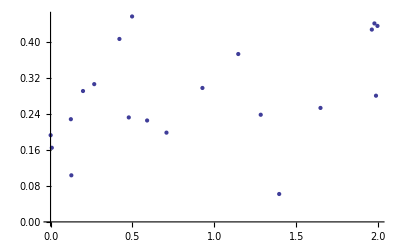

```mathematica
ListPlot[cosDistVSnorm[numofjournals,"z",1,1][1][1,2]]
```

## 引用誌の引用を偏らせる(Zipf;2000)

雑誌数を2000にする

```mathematica
numofjournals=2000
```

2000

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

各雑誌からの引用数を偏らせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(citedBase[numofjournals,"z",1,1]=Round[Table[numofjournals zipFF[n,1,1]/10,{n,numofjournals}]//N])//Dimensions
```

{2000}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
(*randomOrder[numofjournals]*)
```

```mathematica
(*citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]]*)
```

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab[numofjournals,"z",1,1]=Table[citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{2000,2000}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab[numofjournals,"z",1,1]=nextMaxSelf[citedcitingTab[numofjournals,"z",1,1]])//Dimensions
```

{2000,2000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]=standerdizeSum[citedcitingNextMaxSelfTab[numofjournals,"z",1,1]]//N)//Dimensions
```

{2000,2000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]]//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]=PrincipalComponents[citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]];
```

第1、2、3軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]]
```

-Graphics3D-

各軸の値(PC)を正規化

```mathematica
citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]=Transpose[Map[Normalize[#]&,Transpose[citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]]];
```

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
(cosDistList[numofjournals,"z",1,1][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]])//Dimensions
```

{2000}

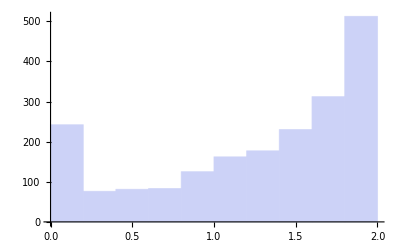

```mathematica
Histogram[cosDistList[numofjournals,"z",1,1][1]]
```

PC1、PC2平面における各ベクトルのノルム

```mathematica
(norm[numofjournals,"z",1,1][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]])//Dimensions
```

{2000}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm[numofjournals,"z",1,1][1][1,2]=Transpose[{cosDistList[numofjournals,"z",1,1][1],norm[numofjournals,"z",1,1][1,2]}])//Dimensions
```

{2000,2}

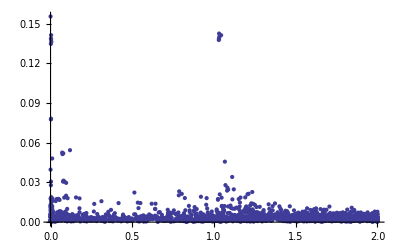

```mathematica
ListPlot[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],PlotRange->All]
```

Fourierのために補間

```mathematica
iplist=ipf[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],1000,0.2,selfconvolve[2]];
```

```mathematica
iplist=ipf[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],1000,0.2,Mean];
```

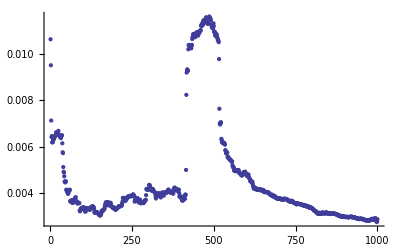

```mathematica
ListPlot[iplist,PlotRange->All]
```

```mathematica
Kurtosis[iplist]
```

6.11821

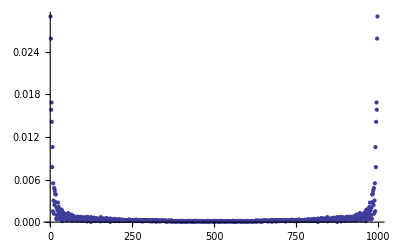

```mathematica
ListPlot[Drop[Abs[Fourier[iplist]],1],PlotRange->All]
```

```mathematica
(iplist//Max)/(iplist//Mean)
```

2.54068

全次元における第1軸からのコサイン距離

```mathematica
(cosDistList[numofjournals,"z",1,1][1,"all"]=Map[CosineDistance[#,Prepend[Table[0,{numofjournals-1}],1]]&,citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]])//Dimensions
```

{2000}

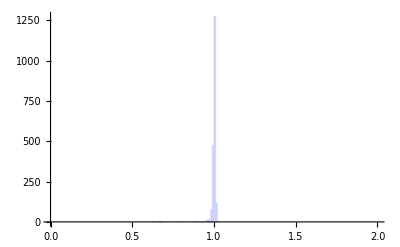

```mathematica
Histogram[cosDistList[numofjournals,"z",1,1][1,"all"],{0,2,0.01}]
```

全次元における第1軸からのコサイン距離の尖度

```mathematica
Kurtosis[cosDistList[numofjournals,"z",1,1][1,"all"]]
```

174.797

## 引用誌の引用を偏らせる(Zipf;6000)

雑誌数を6000にする

```mathematica
numofjournals=6000
```

6000

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

各雑誌からの引用数を偏らせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(citedBase[numofjournals,"z",1,1]=Round[Table[numofjournals zipFF[n,1,1]/10,{n,numofjournals}]//N])//Dimensions
```

{6000}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
(*randomOrder[numofjournals]*)
```

```mathematica
(*citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]]*)
```

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab[numofjournals,"z",1,1]=Table[citedBase[numofjournals,"z",1,1][[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{6000,6000}

もし、自誌被引用数が被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab[numofjournals,"z",1,1]=nextMaxSelf[citedcitingTab[numofjournals,"z",1,1]])//Dimensions
```

{6000,6000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]=standerdizeSum[citedcitingNextMaxSelfTab[numofjournals,"z",1,1]]//N)//Dimensions
```

{6000,6000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]]//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]=PrincipalComponents[citedcitingNextMaxSelfTabST[numofjournals,"z",1,1]];
```

第1、2、3軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]]
```

-Graphics3D-

各軸の値(PC)を正規化

```mathematica
citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]=Transpose[Map[Normalize[#]&,Transpose[citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]]]];
```

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
(cosDistList[numofjournals,"z",1,1][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]])//Dimensions
```

{6000}

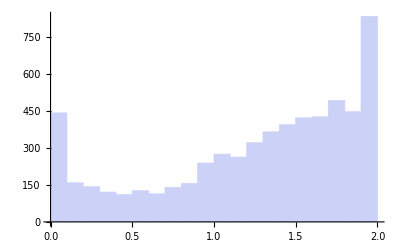

```mathematica
Histogram[cosDistList[numofjournals,"z",1,1][1]]
```

PC1、PC2平面における各ベクトルのノルム

```mathematica
(norm[numofjournals,"z",1,1][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]])//Dimensions
```

{6000}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm[numofjournals,"z",1,1][1][1,2]=Transpose[{cosDistList[numofjournals,"z",1,1][1],norm[numofjournals,"z",1,1][1,2]}])//Dimensions
```

{6000,2}

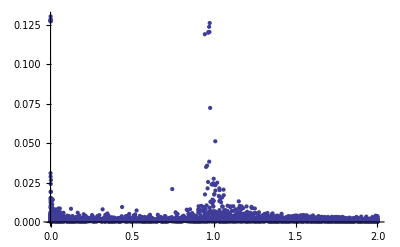

```mathematica
ListPlot[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],PlotRange->All]
```

Fourierのために補間

```mathematica
iplist=ipf[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],1000,0.2,selfconvolve[2]];
```

```mathematica
iplist=ipf[cosDistVSnorm[numofjournals,"z",1,1][1][1,2],1000,0.2,Mean];
```

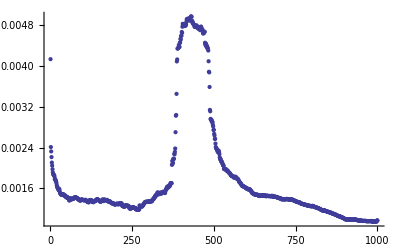

```mathematica
ListPlot[iplist,PlotRange->All]
```

```mathematica
Kurtosis[iplist]
```

6.50553

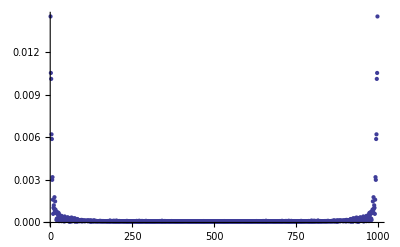

```mathematica
ListPlot[Drop[Abs[Fourier[iplist]],1],PlotRange->All]
```

```mathematica
(iplist//Max)/(iplist//Mean)
```

2.8331

全次元における第1軸からのコサイン距離

```mathematica
(cosDistList[numofjournals,"z",1,1][1,"all"]=Map[CosineDistance[#,Prepend[Table[0,{numofjournals-1}],1]]&,citedcitingNextMaxSelfTabSTPCATrSt[numofjournals,"z",1,1]])//Dimensions
```

{6000}

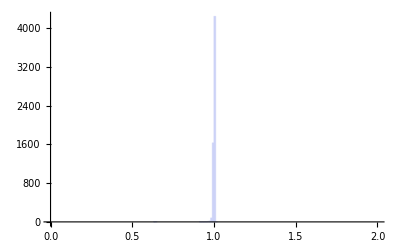

```mathematica
Histogram[cosDistList[numofjournals,"z",1,1][1,"all"],{0,2,0.01}]
```

全次元における第1軸からのコサイン距離の尖度

```mathematica
Kurtosis[cosDistList[numofjournals,"z",1,1][1,"all"]]
```

674.609

全次元における各ベクトルのノルム

```mathematica
(norm[numofjournals,"z",1,1]["all"]=Map[Norm[#]&,citedcitingNextMaxSelfTabSTPCA[numofjournals,"z",1,1]])//Dimensions
```

{6000}

全次元における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm[numofjournals,"z",1,1][1][1,"all"]=Transpose[{cosDistList[numofjournals,"z",1,1][1,"all"],norm[numofjournals,"z",1,1]["all"]}])//Dimensions
```

{6000,2}

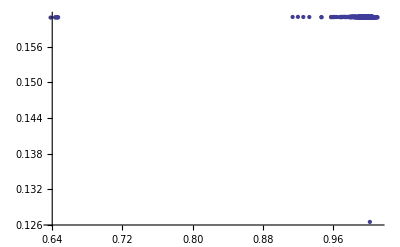

```mathematica
ListPlot[cosDistVSnorm[numofjournals,"z",1,1][1][1,"all"],PlotRange->All]
```

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;ミニサイズ)

雑誌数を20にする

```mathematica
numofjournals=20
```

20

正規分布

```mathematica
Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N
```

{0.012703,0.0138992,0.0150569,0.0161486,0.0171472,0.0180263,0.018762,0.0193334,0.019724,0.0199222,0.0199222,0.019724,0.0193334,0.018762,0.0180263,0.0171472,0.0161486,0.0150569,0.0138992,0.012703}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
citedNumOfJournals["n",numofjournals]=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]]
```

{21,19,19,22,22,23,27,13,28,24,21,19,19,21,21,19,22,30,22,16}

```mathematica
citedBase["n",numofjournals]=citedNumOfJournals["n",numofjournals]
```

{21,19,19,22,22,23,27,13,28,24,21,19,19,21,21,19,22,30,22,16}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
randomOrder[numofjournals]
```

{19,10,12,15,3,18,7,5,13,14,8,16,1,6,9,11,17,2,4,20}

```mathematica
citedBase["n",numofjournals][[randomOrder[numofjournals]]]
```

{28,19,21,19,16,22,23,24,21,21,21,19,22,19,27,22,30,19,13,22}

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab["n",numofjournals]=Table[citedBase["n",numofjournals][[randomOrder[numofjournals]]],{numofjournals}])//TableForm
```

21 | 16 | 24 | 19 | 21 | 19 | 23 | 19 | 21 | 30 | 21 | 19 | 28 | 22 | 22 | 22 | 22 | 19 | 27 | 13
22 | 21 | 19 | 16 | 21 | 22 | 24 | 21 | 19 | 21 | 22 | 23 | 30 | 27 | 19 | 28 | 19 | 19 | 13 | 22
27 | 21 | 19 | 16 | 19 | 13 | 19 | 21 | 19 | 21 | 22 | 28 | 21 | 19 | 30 | 23 | 22 | 24 | 22 | 22
22 | 19 | 21 | 27 | 28 | 21 | 30 | 16 | 22 | 19 | 23 | 19 | 22 | 24 | 21 | 19 | 19 | 21 | 22 | 13
23 | 24 | 19 | 13 | 21 | 22 | 21 | 19 | 22 | 27 | 22 | 19 | 19 | 21 | 19 | 28 | 22 | 21 | 16 | 30
24 | 22 | 28 | 22 | 23 | 19 | 21 | 21 | 30 | 19 | 19 | 19 | 19 | 16 | 21 | 13 | 21 | 22 | 27 | 22
19 | 23 | 21 | 19 | 22 | 21 | 19 | 19 | 16 | 22 | 24 | 30 | 21 | 27 | 19 | 22 | 13 | 28 | 21 | 22
19 | 28 | 30 | 19 | 21 | 22 | 13 | 22 | 27 | 21 | 19 | 22 | 21 | 21 | 19 | 22 | 24 | 19 | 23 | 16
16 | 22 | 28 | 21 | 22 | 21 | 22 | 19 | 19 | 21 | 19 | 30 | 13 | 22 | 24 | 27 | 19 | 21 | 23 | 19
23 | 21 | 19 | 22 | 24 | 19 | 22 | 28 | 22 | 30 | 27 | 22 | 19 | 21 | 19 | 21 | 16 | 19 | 13 | 21
22 | 21 | 22 | 16 | 27 | 13 | 22 | 19 | 19 | 19 | 21 | 22 | 19 | 21 | 21 | 19 | 24 | 23 | 30 | 28
21 | 30 | 22 | 23 | 22 | 19 | 22 | 16 | 21 | 24 | 28 | 19 | 19 | 19 | 13 | 21 | 22 | 27 | 21 | 19
19 | 13 | 21 | 21 | 21 | 19 | 21 | 30 | 19 | 23 | 28 | 19 | 16 | 22 | 22 | 27 | 19 | 22 | 24 | 22
19 | 21 | 19 | 16 | 23 | 30 | 19 | 22 | 27 | 24 | 19 | 21 | 22 | 13 | 19 | 21 | 22 | 21 | 22 | 28
19 | 21 | 21 | 22 | 23 | 24 | 16 | 19 | 28 | 22 | 19 | 19 | 19 | 27 | 13 | 22 | 22 | 21 | 30 | 21
30 | 22 | 21 | 19 | 19 | 19 | 27 | 24 | 19 | 21 | 22 | 21 | 22 | 22 | 23 | 13 | 28 | 21 | 19 | 16
21 | 21 | 22 | 23 | 27 | 19 | 28 | 19 | 21 | 16 | 19 | 21 | 19 | 24 | 22 | 30 | 13 | 22 | 19 | 22
22 | 23 | 22 | 19 | 30 | 21 | 22 | 19 | 19 | 16 | 21 | 21 | 28 | 21 | 13 | 19 | 24 | 19 | 22 | 27
23 | 13 | 21 | 19 | 21 | 21 | 22 | 28 | 22 | 16 | 27 | 19 | 22 | 19 | 22 | 19 | 21 | 30 | 19 | 24
19 | 22 | 21 | 21 | 21 | 19 | 16 | 22 | 24 | 19 | 22 | 27 | 30 | 23 | 19 | 19 | 22 | 28 | 21 | 13

```mathematica
Map[Tr[#]&,citedcitingTab["n",numofjournals]]
```

{428,428,428,428,428,428,428,428,428,428,428,428,428,428,428,428,428,428,428,428}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab["n",numofjournals]=nextMaxSelf[citedcitingTab["n",numofjournals]])//TableForm
```

21 | 16 | 24 | 19 | 21 | 19 | 23 | 19 | 21 | 30 | 21 | 19 | 28 | 22 | 22 | 22 | 22 | 19 | 27 | 13
22 | 21 | 19 | 16 | 21 | 22 | 24 | 21 | 19 | 21 | 22 | 23 | 30 | 27 | 19 | 28 | 19 | 19 | 13 | 22
27 | 21 | 19 | 16 | 19 | 13 | 19 | 21 | 19 | 21 | 22 | 28 | 21 | 19 | 30 | 23 | 22 | 24 | 22 | 22
22 | 19 | 21 | 27 | 28 | 21 | 30 | 16 | 22 | 19 | 23 | 19 | 22 | 24 | 21 | 19 | 19 | 21 | 22 | 13
23 | 24 | 19 | 13 | 21 | 22 | 21 | 19 | 22 | 27 | 22 | 19 | 19 | 21 | 19 | 28 | 22 | 21 | 16 | 30
24 | 22 | 28 | 22 | 23 | 19 | 21 | 21 | 30 | 19 | 19 | 19 | 19 | 16 | 21 | 13 | 21 | 22 | 27 | 22
19 | 23 | 21 | 19 | 22 | 21 | 19 | 19 | 16 | 22 | 24 | 30 | 21 | 27 | 19 | 22 | 13 | 28 | 21 | 22
19 | 28 | 30 | 19 | 21 | 22 | 13 | 22 | 27 | 21 | 19 | 22 | 21 | 21 | 19 | 22 | 24 | 19 | 23 | 16
16 | 22 | 28 | 21 | 22 | 21 | 22 | 19 | 19 | 21 | 19 | 30 | 13 | 22 | 24 | 27 | 19 | 21 | 23 | 19
23 | 21 | 19 | 22 | 24 | 19 | 22 | 28 | 22 | 28 | 27 | 22 | 19 | 21 | 19 | 21 | 16 | 19 | 13 | 21
22 | 21 | 22 | 16 | 27 | 13 | 22 | 19 | 19 | 19 | 21 | 22 | 19 | 21 | 21 | 19 | 24 | 23 | 30 | 28
21 | 30 | 22 | 23 | 22 | 19 | 22 | 16 | 21 | 24 | 28 | 19 | 19 | 19 | 13 | 21 | 22 | 27 | 21 | 19
19 | 13 | 21 | 21 | 21 | 19 | 21 | 30 | 19 | 23 | 28 | 19 | 16 | 22 | 22 | 27 | 19 | 22 | 24 | 22
19 | 21 | 19 | 16 | 23 | 30 | 19 | 22 | 27 | 24 | 19 | 21 | 22 | 13 | 19 | 21 | 22 | 21 | 22 | 28
19 | 21 | 21 | 22 | 23 | 24 | 16 | 19 | 28 | 22 | 19 | 19 | 19 | 27 | 13 | 22 | 22 | 21 | 30 | 21
30 | 22 | 21 | 19 | 19 | 19 | 27 | 24 | 19 | 21 | 22 | 21 | 22 | 22 | 23 | 13 | 28 | 21 | 19 | 16
21 | 21 | 22 | 23 | 27 | 19 | 28 | 19 | 21 | 16 | 19 | 21 | 19 | 24 | 22 | 30 | 13 | 22 | 19 | 22
22 | 23 | 22 | 19 | 30 | 21 | 22 | 19 | 19 | 16 | 21 | 21 | 28 | 21 | 13 | 19 | 24 | 19 | 22 | 27
23 | 13 | 21 | 19 | 21 | 21 | 22 | 28 | 22 | 16 | 27 | 19 | 22 | 19 | 22 | 19 | 21 | 30 | 19 | 24
19 | 22 | 21 | 21 | 21 | 19 | 16 | 22 | 24 | 19 | 22 | 27 | 30 | 23 | 19 | 19 | 22 | 28 | 21 | 13

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST["n",numofjournals]=standerdizeSum[citedcitingNextMaxSelfTab["n",numofjournals]]//N)//TableForm
```

0.0490654 | 0.0373832 | 0.0560748 | 0.0443925 | 0.0490654 | 0.0443925 | 0.0537383 | 0.0443925 | 0.0490654 | 0.0700935 | 0.0490654 | 0.0443925 | 0.0654206 | 0.0514019 | 0.0514019 | 0.0514019 | 0.0514019 | 0.0443925 | 0.0630841 | 0.0303738
0.0514019 | 0.0490654 | 0.0443925 | 0.0373832 | 0.0490654 | 0.0514019 | 0.0560748 | 0.0490654 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0537383 | 0.0700935 | 0.0630841 | 0.0443925 | 0.0654206 | 0.0443925 | 0.0443925 | 0.0303738 | 0.0514019
0.0630841 | 0.0490654 | 0.0443925 | 0.0373832 | 0.0443925 | 0.0303738 | 0.0443925 | 0.0490654 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0654206 | 0.0490654 | 0.0443925 | 0.0700935 | 0.0537383 | 0.0514019 | 0.0560748 | 0.0514019 | 0.0514019
0.0514019 | 0.0443925 | 0.0490654 | 0.0630841 | 0.0654206 | 0.0490654 | 0.0700935 | 0.0373832 | 0.0514019 | 0.0443925 | 0.0537383 | 0.0443925 | 0.0514019 | 0.0560748 | 0.0490654 | 0.0443925 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0303738
0.0537383 | 0.0560748 | 0.0443925 | 0.0303738 | 0.0490654 | 0.0514019 | 0.0490654 | 0.0443925 | 0.0514019 | 0.0630841 | 0.0514019 | 0.0443925 | 0.0443925 | 0.0490654 | 0.0443925 | 0.0654206 | 0.0514019 | 0.0490654 | 0.0373832 | 0.0700935
0.0560748 | 0.0514019 | 0.0654206 | 0.0514019 | 0.0537383 | 0.0443925 | 0.0490654 | 0.0490654 | 0.0700935 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0373832 | 0.0490654 | 0.0303738 | 0.0490654 | 0.0514019 | 0.0630841 | 0.0514019
0.0443925 | 0.0537383 | 0.0490654 | 0.0443925 | 0.0514019 | 0.0490654 | 0.0443925 | 0.0443925 | 0.0373832 | 0.0514019 | 0.0560748 | 0.0700935 | 0.0490654 | 0.0630841 | 0.0443925 | 0.0514019 | 0.0303738 | 0.0654206 | 0.0490654 | 0.0514019
0.0443925 | 0.0654206 | 0.0700935 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0303738 | 0.0514019 | 0.0630841 | 0.0490654 | 0.0443925 | 0.0514019 | 0.0490654 | 0.0490654 | 0.0443925 | 0.0514019 | 0.0560748 | 0.0443925 | 0.0537383 | 0.0373832
0.0373832 | 0.0514019 | 0.0654206 | 0.0490654 | 0.0514019 | 0.0490654 | 0.0514019 | 0.0443925 | 0.0443925 | 0.0490654 | 0.0443925 | 0.0700935 | 0.0303738 | 0.0514019 | 0.0560748 | 0.0630841 | 0.0443925 | 0.0490654 | 0.0537383 | 0.0443925
0.0539906 | 0.0492958 | 0.0446009 | 0.0516432 | 0.056338 | 0.0446009 | 0.0516432 | 0.0657277 | 0.0516432 | 0.0657277 | 0.0633803 | 0.0516432 | 0.0446009 | 0.0492958 | 0.0446009 | 0.0492958 | 0.0375587 | 0.0446009 | 0.0305164 | 0.0492958
0.0514019 | 0.0490654 | 0.0514019 | 0.0373832 | 0.0630841 | 0.0303738 | 0.0514019 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0443925 | 0.0490654 | 0.0490654 | 0.0443925 | 0.0560748 | 0.0537383 | 0.0700935 | 0.0654206
0.0490654 | 0.0700935 | 0.0514019 | 0.0537383 | 0.0514019 | 0.0443925 | 0.0514019 | 0.0373832 | 0.0490654 | 0.0560748 | 0.0654206 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0303738 | 0.0490654 | 0.0514019 | 0.0630841 | 0.0490654 | 0.0443925
0.0443925 | 0.0303738 | 0.0490654 | 0.0490654 | 0.0490654 | 0.0443925 | 0.0490654 | 0.0700935 | 0.0443925 | 0.0537383 | 0.0654206 | 0.0443925 | 0.0373832 | 0.0514019 | 0.0514019 | 0.0630841 | 0.0443925 | 0.0514019 | 0.0560748 | 0.0514019
0.0443925 | 0.0490654 | 0.0443925 | 0.0373832 | 0.0537383 | 0.0700935 | 0.0443925 | 0.0514019 | 0.0630841 | 0.0560748 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0303738 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0490654 | 0.0514019 | 0.0654206
0.0443925 | 0.0490654 | 0.0490654 | 0.0514019 | 0.0537383 | 0.0560748 | 0.0373832 | 0.0443925 | 0.0654206 | 0.0514019 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0630841 | 0.0303738 | 0.0514019 | 0.0514019 | 0.0490654 | 0.0700935 | 0.0490654
0.0700935 | 0.0514019 | 0.0490654 | 0.0443925 | 0.0443925 | 0.0443925 | 0.0630841 | 0.0560748 | 0.0443925 | 0.0490654 | 0.0514019 | 0.0490654 | 0.0514019 | 0.0514019 | 0.0537383 | 0.0303738 | 0.0654206 | 0.0490654 | 0.0443925 | 0.0373832
0.0490654 | 0.0490654 | 0.0514019 | 0.0537383 | 0.0630841 | 0.0443925 | 0.0654206 | 0.0443925 | 0.0490654 | 0.0373832 | 0.0443925 | 0.0490654 | 0.0443925 | 0.0560748 | 0.0514019 | 0.0700935 | 0.0303738 | 0.0514019 | 0.0443925 | 0.0514019
0.0514019 | 0.0537383 | 0.0514019 | 0.0443925 | 0.0700935 | 0.0490654 | 0.0514019 | 0.0443925 | 0.0443925 | 0.0373832 | 0.0490654 | 0.0490654 | 0.0654206 | 0.0490654 | 0.0303738 | 0.0443925 | 0.0560748 | 0.0443925 | 0.0514019 | 0.0630841
0.0537383 | 0.0303738 | 0.0490654 | 0.0443925 | 0.0490654 | 0.0490654 | 0.0514019 | 0.0654206 | 0.0514019 | 0.0373832 | 0.0630841 | 0.0443925 | 0.0514019 | 0.0443925 | 0.0514019 | 0.0443925 | 0.0490654 | 0.0700935 | 0.0443925 | 0.0560748
0.0443925 | 0.0514019 | 0.0490654 | 0.0490654 | 0.0490654 | 0.0443925 | 0.0373832 | 0.0514019 | 0.0560748 | 0.0443925 | 0.0514019 | 0.0630841 | 0.0700935 | 0.0537383 | 0.0443925 | 0.0443925 | 0.0514019 | 0.0654206 | 0.0490654 | 0.0303738

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST["n",numofjournals]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA["n",numofjournals]=PrincipalComponents[citedcitingNextMaxSelfTabST["n",numofjournals]];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]]
```

-Graphics3D-

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
cosDistList["n",numofjournals][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]
```

{0.581348,1.98432,1.78583,0.853335,1.46067,0.0104584,1.97905,0.0422842,1.69208,1.99995,0.0648247,0.0525056,1.99877,0.668443,0.13954,0.896655,1.99287,0.298276,1.77011,0.497303}

PC1、PC2平面における各ベクトルのノルム

```mathematica
norm["n",numofjournals][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]
```

{0.0176505,0.0243866,0.0164562,0.0237896,0.0318438,0.0302374,0.0155125,0.0264015,0.00621668,0.0191978,0.00843785,0.00918476,0.0179699,0.0286748,0.0276595,0.027089,0.0179651,0.0130414,0.013957,0.0176833}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
cosDistVSnorm["n",numofjournals][1][1,2]=Transpose[{cosDistList["n",numofjournals][1],norm["n",numofjournals][1,2]}]
```

{{0.581348,0.0176505},{1.98432,0.0243866},{1.78583,0.0164562},{0.853335,0.0237896},{1.46067,0.0318438},{0.0104584,0.0302374},{1.97905,0.0155125},{0.0422842,0.0264015},{1.69208,0.00621668},{1.99995,0.0191978},{0.0648247,0.00843785},{0.0525056,0.00918476},{1.99877,0.0179699},{0.668443,0.0286748},{0.13954,0.0276595},{0.896655,0.027089},{1.99287,0.0179651},{0.298276,0.0130414},{1.77011,0.013957},{0.497303,0.0176833}}

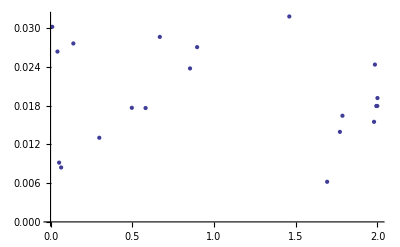

```mathematica
ListPlot[cosDistVSnorm["n",numofjournals][1][1,2]]
```

```mathematica
numofjournals
```

20

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;2000誌)

雑誌数を2000にする

```mathematica
numofjournals=2000
```

2000

正規分布

```mathematica
Table[PDF[NormalDistribution[2000,2000],x],{x,1,3999,2}]//N//Dimensions
```

{2000}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
(citedNumOfJournals["n",numofjournals]=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]])//Dimensions
```

{2000}

```mathematica
(citedBase["n",numofjournals]=citedNumOfJournals["n",numofjournals])//Dimensions
```

{2000}

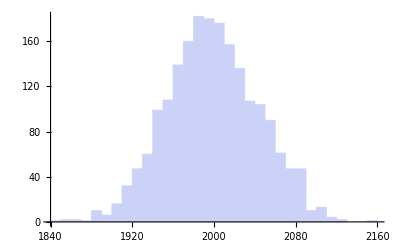

```mathematica
Histogram[citedBase["n",numofjournals]]
```

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
(*randomOrder[numofjournals]*)
```

```mathematica
(*citedBase["n",numofjournals][[randomOrder[numofjournals]]]*)
```

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab["n",numofjournals]=Table[citedBase["n",numofjournals][[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{2000,2000}

```mathematica
Map[Tr[#]&,citedcitingTab["n",numofjournals]]//Union
```

{3996635}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab["n",numofjournals]=nextMaxSelf[citedcitingTab["n",numofjournals]])//Dimensions
```

{2000,2000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST["n",numofjournals]=standerdizeSum[citedcitingNextMaxSelfTab["n",numofjournals]]//N)//Dimensions
```

{2000,2000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST["n",numofjournals]]//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA["n",numofjournals]=PrincipalComponents[citedcitingNextMaxSelfTabST["n",numofjournals]];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]]
```

-Graphics3D-

各軸の値(PC)を正規化

```mathematica
citedcitingNextMaxSelfTabSTPCATrSt["n",numofjournals]=Transpose[Map[Normalize[#]&,Transpose[citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]]];
```

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
(cosDistList["n",numofjournals][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]])//Dimensions
```

{2000}

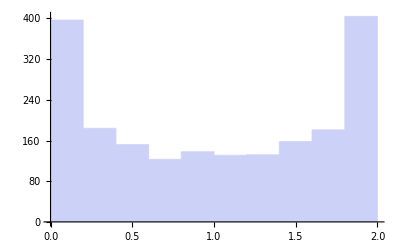

```mathematica
Histogram[cosDistList["n",numofjournals][1]]
```

PC1、PC2平面における各ベクトルのノルム

```mathematica
(norm["n",numofjournals][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]])//Dimensions
```

{2000}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm["n",numofjournals][1][1,2]=Transpose[{cosDistList["n",numofjournals][1],norm["n",numofjournals][1,2]}])//Dimensions
```

{2000,2}

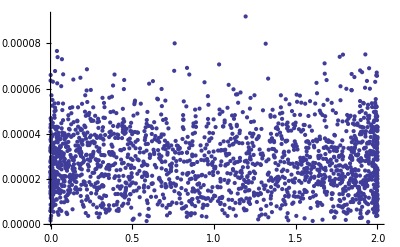

```mathematica
ListPlot[cosDistVSnorm["n",numofjournals][1][1,2],PlotRange->All]
```

```mathematica
iplist=ipf[cosDistVSnorm["n",numofjournals][1][1,2],1000,0.1,selfconvolve[1]];
```

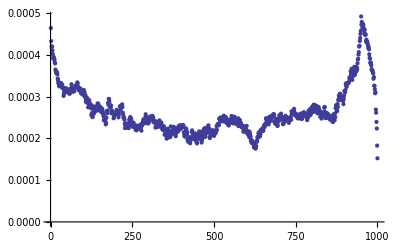

```mathematica
ListPlot[iplist]
```

```mathematica
Kurtosis[iplist]
```

5.498

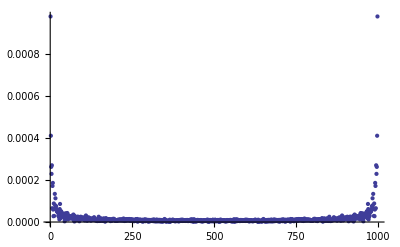

```mathematica
ListPlot[Drop[Abs[Fourier[iplist]],1],PlotRange->All]
```

```mathematica
(iplist//Max)/(iplist//Mean)
```

1.86324

全次元における第1軸からのコサイン距離

```mathematica
(cosDistList["n",numofjournals][1,"all"]=Map[CosineDistance[#,Prepend[Table[0,{1999}],1]]&,citedcitingNextMaxSelfTabSTPCATrSt["n",numofjournals]])//Dimensions
```

{2000}

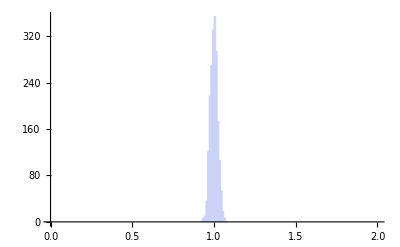

```mathematica
Histogram[cosDistList["n",numofjournals][1,"all"],{0,2,0.01}]
```

全次元における第1軸からのコサイン距離の尖度

```mathematica
Kurtosis[cosDistList["n",numofjournals][1,"all"]]
```

2.91049

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;6000誌)

雑誌数を6000にする

```mathematica
numofjournals=6000
```

6000

正規分布

```mathematica
Table[PDF[NormalDistribution[2000,2000],x],{x,1,3999,2}]//N//Dimensions
```

{2000}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
(citedNumOfJournals["n",numofjournals]=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]])//Dimensions
```

{6000}

```mathematica
(citedBase["n",numofjournals]=citedNumOfJournals["n",numofjournals])//Dimensions
```

{6000}

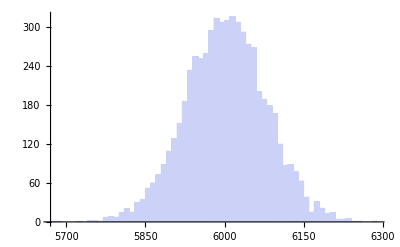

```mathematica
Histogram[citedBase["n",numofjournals]]
```

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
(*randomOrder[numofjournals]*)
```

```mathematica
(*citedBase["n",numofjournals][[randomOrder[numofjournals]]]*)
```

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab["n",numofjournals]=Table[citedBase["n",numofjournals][[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{6000,6000}

```mathematica
Map[Tr[#]&,citedcitingTab["n",numofjournals]]//Union
```

{36012183}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab["n",numofjournals]=nextMaxSelf[citedcitingTab["n",numofjournals]])//Dimensions
```

{6000,6000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST["n",numofjournals]=standerdizeSum[citedcitingNextMaxSelfTab["n",numofjournals]]//N)//Dimensions
```

{6000,6000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST["n",numofjournals]]//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA["n",numofjournals]=PrincipalComponents[citedcitingNextMaxSelfTabST["n",numofjournals]];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]]
```

-Graphics3D-

各軸の値(PC)を正規化

```mathematica
citedcitingNextMaxSelfTabSTPCATrSt["n",numofjournals]=Transpose[Map[Normalize[#]&,Transpose[citedcitingNextMaxSelfTabSTPCA["n",numofjournals]]]];
```

PC1、PC2平面における第1軸からのコサイン距離

```mathematica
(cosDistList["n",numofjournals][1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]])//Dimensions
```

{6000}

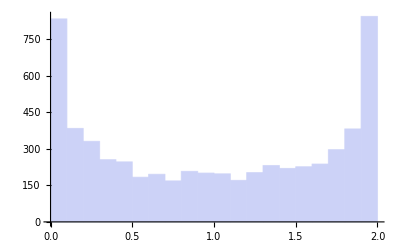

```mathematica
Histogram[cosDistList["n",numofjournals][1]]
```

PC1、PC2平面における各ベクトルのノルム

```mathematica
(norm["n",numofjournals][1,2]=Map[Norm[#[[{1,2}]]]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]])//Dimensions
```

{6000}

PC1、PC2平面における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm["n",numofjournals][1][1,2]=Transpose[{cosDistList["n",numofjournals][1],norm["n",numofjournals][1,2]}])//Dimensions
```

{6000,2}

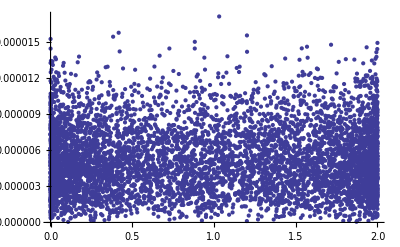

```mathematica
ListPlot[cosDistVSnorm["n",numofjournals][1][1,2],PlotRange->All]
```

```mathematica
iplist=ipf[cosDistVSnorm["n",numofjournals][1][1,2],1000,0.1,selfconvolve[1]];
```

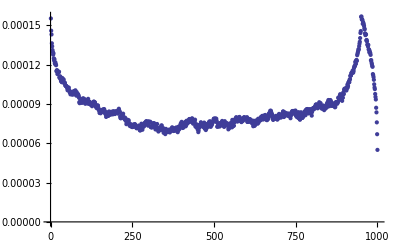

```mathematica
ListPlot[iplist]
```

```mathematica
Kurtosis[iplist]
```

6.44515

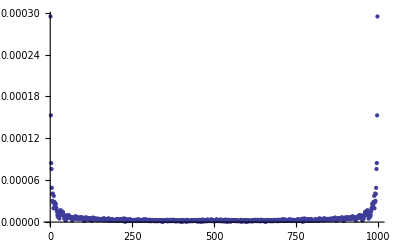

```mathematica
ListPlot[Drop[Abs[Fourier[iplist]],1],PlotRange->All]
```

```mathematica
(iplist//Max)/(iplist//Mean)
```

1.81341

全次元における第1軸からのコサイン距離

```mathematica
(cosDistList["n",numofjournals][1,"all"]=Map[CosineDistance[#,Prepend[Table[0,{numofjournals-1}],1]]&,citedcitingNextMaxSelfTabSTPCATrSt["n",numofjournals]])//Dimensions
```

{6000}

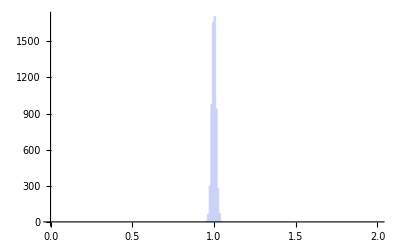

```mathematica
Histogram[cosDistList["n",numofjournals][1,"all"],{0,2,0.01}]
```

全次元における第1軸からのコサイン距離の尖度

```mathematica
Kurtosis[cosDistList["n",numofjournals][1,"all"]]
```

3.01117

全次元における各ベクトルのノルム

```mathematica
(norm["n",numofjournals]["all"]=Map[Norm[#]&,citedcitingNextMaxSelfTabSTPCA["n",numofjournals]])//Dimensions
```

{6000}

全次元における第1軸からのコサイン距離 vs. ノルム

```mathematica
(cosDistVSnorm["n",numofjournals][1,"all"]=Transpose[{cosDistList["n",numofjournals][1,"all"],norm["n",numofjournals]["all"]}])//Dimensions
```

{6000,2}

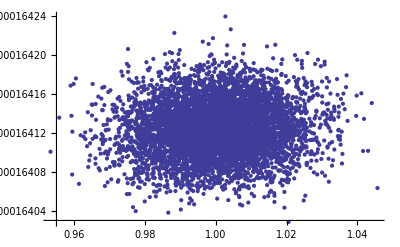

```mathematica
ListPlot[cosDistVSnorm["n",numofjournals][1,"all"],PlotRange->All]
```

## Zipf Citation Model (ミニサイズ)

### model function

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

### application

雑誌数を20に

```mathematica
numOfJournals=20
```

20

各雑誌の被引用数がzipfの法則に従うとする

```mathematica
citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,1,1],{n,numOfJournals}]//N]
```

{20,10,7,5,4,4,3,3,3,2,2,2,2,2,2,2,2,2,2,1}

何番目の雑誌から引用されるかはランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}])
```

{{18,19,18,19,12,4,6,3,5,9,13,4,11,3,15,5,4,3,7,3},{2,7,15,8,9,12,18,8,18,5},{14,15,9,16,19,16,15},{7,13,5,1,5},{6,19,6,7},{18,15,10,19},{3,2,14},{14,7,17},{20,13,13},{20,19},{7,13},{14,12},{14,4},{11,15},{15,1},{11,8},{9,7},{5,16},{7,17},{11}}

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited])//TableForm
```

0 | 0 | 4 | 3 | 2 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 2 | 2 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]])//TableForm
```

0. | 0. | 0.2 | 0.15 | 0.1 | 0.05 | 0.05 | 0. | 0.05 | 0. | 0.05 | 0.05 | 0.05 | 0. | 0.05 | 0. | 0. | 0.1 | 0.1 | 0.
0. | 0.1 | 0. | 0. | 0.1 | 0. | 0.1 | 0.2 | 0.1 | 0. | 0. | 0.1 | 0. | 0. | 0.1 | 0. | 0. | 0.2 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.142857 | 0. | 0. | 0. | 0. | 0.142857 | 0.285714 | 0.285714 | 0. | 0. | 0.142857 | 0.
0.2 | 0. | 0. | 0. | 0.4 | 0. | 0.2 | 0. | 0. | 0. | 0. | 0. | 0.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.5 | 0.25 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0. | 0.25 | 0.25 | 0.
0. | 0.333333 | 0.333333 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.333333 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.333333 | 0. | 0. | 0. | 0. | 0. | 0. | 0.333333 | 0. | 0. | 0.333333 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.666667 | 0. | 0. | 0. | 0. | 0. | 0. | 0.333333
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0.5
0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST])//TableForm
```

0.0228383 | 0.0617838 | 0.0482968 | 0.0146819 | 0.00893968 | 0.0620739 | 0.0805406 | 0.0590565 | 0.0832291 | 0.0788867 | 0.0367679 | 0.0148813 | 0.117813 | 0.125012 | 0.0243244 | 0.0978737 | 0.0562888 | 0.0269436 | 0.0131429 | 0.
0.0253408 | 0.0252792 | 0.0289792 | -0.0891551 | 0.0366276 | 0.0334628 | 0.186548 | -0.186982 | 0.0374013 | 0.0440523 | -0.0521835 | 0.0571427 | 0.058042 | 0.0619003 | 0.0129039 | -0.0535279 | -0.0857895 | 0.0364551 | -0.00268927 | 0.
0.0117197 | 0.191347 | 0.141518 | -0.152824 | 0.00658749 | 0.0198347 | 0.0129669 | 0.0576096 | -0.188482 | -0.00981571 | 0.0376078 | 0.114209 | -0.16154 | -0.0321189 | -0.015691 | 0.0353834 | 0.0211422 | 0.0358948 | -0.0308155 | 0.
0.147585 | -0.128557 | 0.129396 | -0.0255728 | 0.284058 | -0.0395718 | -0.0293843 | 0.00492463 | 0.125297 | -0.0296267 | -0.0479097 | -0.15988 | 0.134522 | -0.0475634 | 0.0315313 | -0.0623846 | 0.0465036 | 0.010742 | -0.0264093 | 0.
0.139679 | -0.102183 | 0.0271401 | -0.0650749 | -0.210393 | 0.249626 | 0.0590191 | 0.186852 | 0.287685 | -0.208667 | 0.0102855 | 0.0354092 | -0.112452 | 0.0220767 | -0.0214804 | -0.0300409 | -0.00526406 | -0.00323076 | -0.000561838 | 0.
-0.013216 | 0.12211 | 0.225326 | -0.119618 | -0.192091 | 0.0358194 | 0.0340458 | -0.0488321 | 0.0108946 | 0.0361775 | 0.00601127 | 0.21719 | 0.197636 | -0.0897494 | -0.0688408 | -0.00936455 | 0.0169731 | -0.0230112 | 0.00152625 | 0.
0.0782452 | 0.287188 | -0.156712 | 0.107021 | 0.0133721 | -0.0230924 | 0.083696 | -0.0533544 | 0.115005 | 0.171879 | 0.345536 | -0.0735097 | -0.0545001 | -0.0336668 | 0.00696048 | -0.00897303 | -0.00823399 | -0.0153329 | -0.00423793 | 0.
0.221185 | -0.0238265 | -0.33587 | -0.0650828 | -0.0531134 | -0.02465 | -0.208354 | -0.0589687 | -0.0207362 | 0.0216833 | 0.00501765 | 0.0173068 | -0.0379098 | -0.0541946 | -0.0279432 | -0.0617938 | 0.0336453 | 0.0400976 | 0.028952 | 0.
0.158784 | -0.22002 | 0.300436 | 0.506863 | 0.0404469 | -0.227075 | -0.0213158 | -0.0196053 | -0.0531916 | 0.0126564 | 0.0130043 | 0.0472203 | -0.0650852 | 0.0821471 | -0.0819296 | -0.0418064 | 0.0112597 | -0.00670743 | 0.000548766 | 0.
0.0729204 | 0.0568865 | 0.326168 | 0.230351 | -0.344486 | 0.325224 | -0.131074 | -0.0552432 | -0.125547 | 0.0390558 | -0.0348506 | -0.162308 | 0.0127075 | -0.0286567 | 0.0622305 | 0.00820448 | -0.0154916 | 0.00161881 | 0.00275388 | 0.
0.27852 | -0.424439 | -0.0170395 | 0.156946 | 0.0562026 | -0.208926 | 0.0562181 | 0.0625913 | 0.0215568 | -0.046771 | 0.0180026 | 0.0914703 | 0.00123674 | -0.109047 | 0.087359 | 0.0734447 | -0.0338002 | 0.00413805 | 0.00706791 | 0.
0.106164 | 0.409858 | -0.275887 | 0.164657 | 0.0157446 | -0.0807598 | 0.0375969 | -0.155367 | -0.083044 | -0.342969 | -0.014601 | -0.0233653 | 0.0467584 | 0.0173384 | 0.0102997 | 0.0251896 | 0.00705387 | -0.0126342 | -0.00170682 | 0.
0.106067 | 0.412252 | -0.274367 | 0.175381 | 0.0119551 | -0.0761579 | -0.0279008 | 0.262456 | 0.0133636 | 0.169057 | -0.224735 | 0.0179206 | 0.0143648 | 0.0000491951 | 0.00743788 | -0.0110716 | -0.0239811 | -0.0106665 | -0.00492172 | 0.
-0.501192 | 0.00128074 | 0.0864069 | -0.160473 | -0.0810201 | -0.188587 | -0.0565777 | 0.071074 | -0.076356 | -0.0305352 | 0.0634781 | 0.0911569 | -0.015146 | 0.0596019 | 0.125405 | -0.0757001 | 0.0170153 | -0.0161498 | 0.00557324 | 0.
-0.0729757 | 0.155045 | 0.303926 | -0.345244 | -0.0861896 | -0.380001 | -0.056152 | -0.0165295 | 0.0836556 | -0.0132838 | -0.0598664 | -0.1794 | -0.0544579 | -0.00870107 | -0.0484639 | 0.04534 | -0.022798 | -0.00300113 | 0.0106796 | 0.
-0.48662 | -0.105806 | -0.108915 | 0.0838264 | 0.0455137 | 0.0938851 | 0.131792 | -0.228458 | 0.110434 | 0.096306 | -0.187604 | 0.0155279 | -0.144608 | -0.0387567 | 0.0101356 | 0.0217416 | 0.0394669 | -0.0146934 | 0.00119323 | 0.
0.228003 | -0.291791 | -0.176805 | -0.218519 | -0.0521572 | 0.0572313 | 0.307036 | 0.0900506 | -0.247381 | 0.0253586 | -0.00719394 | -0.128587 | 0.00550364 | 0.0105325 | -0.031325 | -0.022476 | 0.0150548 | -0.0188178 | 0.00657068 | 0.
0.0627596 | 0.102554 | 0.211519 | -0.119377 | 0.545918 | 0.281533 | -0.109168 | 0.0274301 | -0.0592841 | -0.0218853 | 0.0157064 | 0.0382559 | -0.0412501 | 0.00358248 | -0.0062314 | 0.00980118 | -0.0221342 | -0.0206171 | 0.0185317 | 0.
0.254338 | -0.318612 | -0.284981 | -0.209927 | -0.0833014 | 0.0290837 | -0.273663 | -0.116124 | 0.00742517 | 0.0665824 | 0.000366543 | 0.0375381 | 0.0123012 | 0.0815317 | -0.00732005 | 0.0378636 | -0.0154373 | -0.0255316 | -0.021177 | 0.
-0.840146 | -0.210351 | -0.198534 | 0.131142 | 0.0373848 | 0.0610471 | -0.0758689 | 0.117419 | -0.0419254 | -0.05814 | 0.0771606 | -0.0681789 | 0.0860642 | -0.0213178 | -0.0693621 | 0.0222966 | -0.0314737 | 0.0145038 | -0.00402092 | 0.

プロット

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Zipf Citation Model (実践的サイズ)

### model function

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

### application

雑誌数を2000に

```mathematica
numOfJournals=2000
```

2000

各雑誌の被引用数がzipfの法則に従うとする

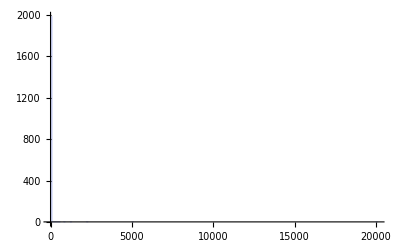

```mathematica
Histogram[(citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,2,10],{n,numOfJournals}]//N])]
```

```mathematica
citedNumOfJournals//Min
```

1

何番目の雑誌から引用されるかは一様にランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited]);
```

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]]);
```

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST]);
```

プロット

```mathematica
Graphics3D[{Map[Point[{#[[50]],#[[51]],#[[52]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Normal Distribution Model (ミニサイズ)

### model function

Normal Distribution

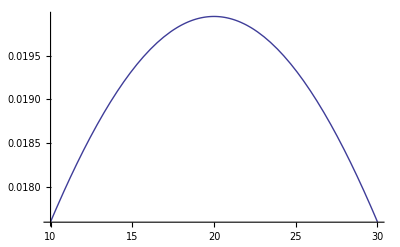

```mathematica
Plot[PDF[NormalDistribution[20,20],x],{x,10,30}]
```

### application

雑誌数を20に

```mathematica
numOfJournals=20
```

20

各雑誌の被引用数が正規分布に従うとする

```mathematica
(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length
```

20

```mathematica
citedNumOfJournals
```

{13,14,16,17,18,19,19,20,20,20,20,20,20,19,19,18,17,16,14,13}

何番目の雑誌から引用されるかはランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

```mathematica
journalCited
```

{{18,10,7,6,12,2,14,14,4,2,19,5,12},{17,16,12,12,20,19,7,15,10,1,7,14,8,11},{2,6,5,12,13,1,20,14,3,2,7,20,8,4,17,15},{20,8,20,7,12,3,11,13,17,6,3,16,16,2,15,6,1},{19,5,12,17,5,2,19,16,6,6,12,18,4,15,6,12,17,1},{13,17,3,4,19,20,18,3,11,18,18,6,9,7,14,15,6,17,18},{19,19,7,12,10,13,3,10,6,6,19,1,11,14,4,12,1,20,12},{19,5,2,1,18,2,7,15,11,14,19,17,15,20,7,1,20,3,7,20},{13,3,11,8,3,14,4,2,15,18,9,7,6,4,15,13,6,18,13,4},{13,8,18,5,17,10,7,2,11,9,9,7,14,15,9,5,6,5,20,6},{5,3,17,20,4,19,3,17,3,12,2,19,11,2,12,9,12,14,10,4},{1,5,3,4,12,17,14,9,5,19,15,10,2,14,3,20,6,15,4,16},{9,20,7,18,4,6,16,5,8,2,9,11,12,11,16,12,14,20,1,10},{1,14,19,19,17,15,1,2,10,20,5,17,13,17,10,1,18,18,3},{18,10,3,8,12,1,6,6,9,4,3,5,18,7,7,11,3,13,20},{11,3,7,3,5,17,1,14,9,7,10,4,4,17,15,6,8,8},{14,18,6,3,18,14,3,5,20,17,3,7,2,8,2,9,1},{5,6,4,9,20,9,8,8,20,7,1,14,11,13,13,11},{13,11,7,4,18,4,2,1,6,7,6,17,7,6},{2,9,17,5,15,14,15,2,9,14,6,3,5}}

```mathematica
Map[Tr[#]&,journalCited]
```

{125,169,149,176,192,236,199,223,186,196,198,194,211,220,164,149,150,159,109,116}

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited])//TableForm
```

2 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 2 | 1 | 0 | 2 | 2 | 2 | 0 | 1 | 0 | 3 | 0 | 0
0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 2 | 2 | 2 | 0 | 2 | 1 | 3 | 0 | 4 | 0
0 | 3 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 3 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 3 | 2 | 1 | 1 | 0 | 3 | 1 | 1 | 1 | 0 | 3 | 1
1 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 1 | 1 | 0 | 2 | 1 | 2 | 2 | 0 | 2 | 0 | 1 | 1
0 | 0 | 0 | 1 | 6 | 0 | 1 | 0 | 2 | 2 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 2 | 1 | 2
1 | 1 | 1 | 2 | 2 | 2 | 0 | 2 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 1
0 | 0 | 2 | 0 | 0 | 1 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 2
0 | 0 | 0 | 3 | 0 | 0 | 4 | 1 | 2 | 3 | 0 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 0
0 | 2 | 0 | 3 | 1 | 1 | 1 | 2 | 2 | 0 | 3 | 0 | 1 | 0 | 3 | 0 | 0 | 2 | 2 | 1
2 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 1
1 | 2 | 3 | 0 | 0 | 1 | 2 | 1 | 3 | 1 | 2 | 4 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
1 | 0 | 3 | 0 | 1 | 1 | 0 | 3 | 1 | 3 | 0 | 2 | 0 | 0 | 1 | 2 | 0 | 2 | 0 | 1
0 | 2 | 2 | 0 | 2 | 1 | 1 | 1 | 0 | 1 | 2 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 1
1 | 1 | 1 | 2 | 0 | 2 | 0 | 1 | 1 | 1 | 0 | 1 | 2 | 2 | 3 | 0 | 2 | 1 | 1 | 0
2 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 0
2 | 3 | 0 | 1 | 1 | 3 | 2 | 0 | 3 | 1 | 2 | 1 | 1 | 3 | 0 | 2 | 0 | 0 | 0 | 1
1 | 2 | 1 | 3 | 0 | 3 | 0 | 1 | 0 | 2 | 0 | 2 | 0 | 0 | 1 | 3 | 4 | 1 | 1 | 0
1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 4 | 2 | 1 | 1 | 1 | 1 | 3 | 0 | 2 | 0 | 0 | 1
0 | 2 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 2 | 1 | 1 | 0 | 0 | 2 | 0 | 0

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]])//TableForm
```

0.0833333 | 0.0416667 | 0.0416667 | 0.0416667 | 0.0416667 | 0.0416667 | 0.0416667 | 0.125 | 0.0833333 | 0.0416667 | 0. | 0.0833333 | 0.0833333 | 0.0833333 | 0. | 0.0416667 | 0. | 0.125 | 0. | 0.
0. | 0.0454545 | 0.0454545 | 0. | 0.0454545 | 0. | 0.0454545 | 0. | 0.0454545 | 0.0454545 | 0.0909091 | 0.0909091 | 0.0909091 | 0. | 0.0909091 | 0.0454545 | 0.136364 | 0. | 0.181818 | 0.
0. | 0.214286 | 0. | 0.0714286 | 0.0714286 | 0. | 0. | 0.0714286 | 0. | 0.0714286 | 0. | 0. | 0. | 0.0714286 | 0.0714286 | 0.0714286 | 0.214286 | 0. | 0.0714286 | 0.
0.0454545 | 0.0454545 | 0.0454545 | 0. | 0. | 0.0454545 | 0. | 0.0454545 | 0.136364 | 0.0909091 | 0.0454545 | 0.0454545 | 0. | 0.136364 | 0.0454545 | 0.0454545 | 0.0454545 | 0. | 0.136364 | 0.0454545
0.0434783 | 0.0869565 | 0.0869565 | 0. | 0.0869565 | 0.0434783 | 0.0434783 | 0.0434783 | 0.0434783 | 0.0434783 | 0. | 0.0869565 | 0.0434783 | 0.0869565 | 0.0869565 | 0. | 0.0869565 | 0. | 0.0434783 | 0.0434783
0. | 0. | 0. | 0.05 | 0.3 | 0. | 0.05 | 0. | 0.1 | 0.1 | 0.05 | 0. | 0. | 0. | 0.05 | 0. | 0.05 | 0.1 | 0.05 | 0.1
0.0526316 | 0.0526316 | 0.0526316 | 0.105263 | 0.105263 | 0.105263 | 0. | 0.105263 | 0.105263 | 0. | 0.0526316 | 0. | 0. | 0. | 0. | 0.105263 | 0.105263 | 0. | 0. | 0.0526316
0. | 0. | 0.142857 | 0. | 0. | 0.0714286 | 0. | 0.142857 | 0.0714286 | 0.0714286 | 0.0714286 | 0. | 0. | 0. | 0.142857 | 0.0714286 | 0.0714286 | 0. | 0. | 0.142857
0. | 0. | 0. | 0.12 | 0. | 0. | 0.16 | 0.04 | 0.08 | 0.12 | 0. | 0.08 | 0.04 | 0.04 | 0.08 | 0.08 | 0.08 | 0.04 | 0.04 | 0.
0. | 0.0833333 | 0. | 0.125 | 0.0416667 | 0.0416667 | 0.0416667 | 0.0833333 | 0.0833333 | 0. | 0.125 | 0. | 0.0416667 | 0. | 0.125 | 0. | 0. | 0.0833333 | 0.0833333 | 0.0416667
0.181818 | 0. | 0. | 0. | 0.181818 | 0. | 0. | 0.0909091 | 0. | 0. | 0. | 0.0909091 | 0. | 0.181818 | 0. | 0.0909091 | 0.0909091 | 0. | 0. | 0.0909091
0.0434783 | 0.0869565 | 0.130435 | 0. | 0. | 0.0434783 | 0.0869565 | 0.0434783 | 0.130435 | 0.0434783 | 0.0869565 | 0.173913 | 0.0434783 | 0. | 0.0869565 | 0. | 0. | 0. | 0. | 0.
0.047619 | 0. | 0.142857 | 0. | 0.047619 | 0.047619 | 0. | 0.142857 | 0.047619 | 0.142857 | 0. | 0.0952381 | 0. | 0. | 0.047619 | 0.0952381 | 0. | 0.0952381 | 0. | 0.047619
0. | 0.0869565 | 0.0869565 | 0. | 0.0869565 | 0.0434783 | 0.0434783 | 0.0434783 | 0. | 0.0434783 | 0.0869565 | 0. | 0.0869565 | 0.0434783 | 0.0434783 | 0.0869565 | 0.0434783 | 0.0434783 | 0.0869565 | 0.0434783
0.0454545 | 0.0454545 | 0.0454545 | 0.0909091 | 0. | 0.0909091 | 0. | 0.0454545 | 0.0454545 | 0.0454545 | 0. | 0.0454545 | 0.0909091 | 0.0909091 | 0.136364 | 0. | 0.0909091 | 0.0454545 | 0.0454545 | 0.
0.125 | 0.0625 | 0. | 0.0625 | 0. | 0.1875 | 0. | 0. | 0.0625 | 0.0625 | 0.0625 | 0.0625 | 0. | 0. | 0.0625 | 0.125 | 0.125 | 0. | 0. | 0.
0.0769231 | 0.115385 | 0. | 0.0384615 | 0.0384615 | 0.115385 | 0.0769231 | 0. | 0.115385 | 0.0384615 | 0.0769231 | 0.0384615 | 0.0384615 | 0.115385 | 0. | 0.0769231 | 0. | 0. | 0. | 0.0384615
0.04 | 0.08 | 0.04 | 0.12 | 0. | 0.12 | 0. | 0.04 | 0. | 0.08 | 0. | 0.08 | 0. | 0. | 0.04 | 0.12 | 0.16 | 0.04 | 0.04 | 0.
0.05 | 0. | 0. | 0.05 | 0.05 | 0.05 | 0. | 0. | 0.2 | 0.1 | 0.05 | 0.05 | 0.05 | 0.05 | 0.15 | 0. | 0.1 | 0. | 0. | 0.05
0. | 0.125 | 0.0625 | 0. | 0. | 0.0625 | 0.0625 | 0.0625 | 0.0625 | 0.0625 | 0.125 | 0. | 0.125 | 0.0625 | 0.0625 | 0. | 0. | 0.125 | 0. | 0.

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST]);
```

プロット

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Normal Distribution Model (実践的サイズ)

### model function

Normal Distribution

```mathematica
normDistBase[n_,m_]:=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[n/m,Sqrt[n/m]],n]]]
```

### application

雑誌数を2000に

```mathematica
numOfJournals=2000
```

2000

各雑誌の被引用数が正規分布に従うとする

```mathematica
citedNumOfJournals
```

{1976,1977,1940,2028,1953,1996,2033,2038,1973,2006,1993,2012,2020,1995,2010,1928,2052,2026,1925,2007,2039,1908,2063,1925,2049,2010,2072,1973,2024,1963,2040,1980,2073,1996,2013,2029,2001,1990,1936,2092,2001,2031,2014,2034,1970,2003,1992,2016,1980,2027,2029,2081,2006,1985,2005,1984,2094,1937,2041,2094,1999,2028,2006,2064,1921,1998,2041,2037,1996,1994,2026,2008,2006,1959,2004,1999,1957,1988,1895,2001,1989,1967,2012,2012,2056,1865,2008,1989,2005,2077,2056,2053,1973,1995,1926,2060,1925,1980,2100,1930,1995,1934,2024,1982,2004,1919,2144,2032,1981,2042,2021,2048,1926,2058,1923,2096,2074,2035,2071,1960,1965,1989,1980,2032,1964,2010,1960,1944,2014,2072,1968,1967,1954,2035,2049,1985,2000,1982,1989,2000,1987,2002,2003,1935,2023,2035,1992,2035,1993,2049,1965,1952,2027,1914,1970,1916,1947,1944,2057,1961,1996,2009,2066,2010,2016,1979,1966,2020,2048,2064,2073,1992,2054,2007,2043,2092,1984,2016,1989,2011,1908,1992,2025,1946,1971,2024,2064,1993,2036,2017,2036,2020,2018,1945,1971,2070,2026,2035,1982,1974,1912,2049,2027,2017,1941,1947,1978,1999,1919,2031,2019,1944,1998,2010,1977,2011,2087,2029,1987,1988,1992,1923,1944,2009,1968,2009,2055,2012,2080,2025,2055,1945,1931,1969,2003,2006,1986,2043,2004,1992,2006,2009,1973,1982,2046,2046,2032,2017,2015,1964,1994,2050,1906,1997,1998,2077,2034,2040,1978,1960,1934,1994,2036,1997,2026,2075,1941,1963,2057,1983,1944,2036,2001,1995,1949,1986,2004,1966,2004,1999,2000,1995,2024,1988,1888,2063,1959,2072,1939,2037,2068,1955,1950,2042,1988,1980,2014,2073,1981,1988,1996,1977,1966,1954,2013,2033,1997,2060,2001,1983,1994,1938,2042,2071,1998,1908,2008,1978,1989,2022,2107,1997,1988,2080,1968,1919,2006,1991,1987,2006,2014,1980,1941,2006,1987,1998,1973,2021,1944,2027,1929,1992,2060,1974,2001,1944,1959,2027,2042,1957,1976,2047,1991,2071,1962,1915,1937,2066,2023,1980,2073,2047,1996,2021,2024,1955,2020,2007,1993,2006,2024,2037,2038,2037,1969,2079,1988,2024,2026,1990,1936,1966,1996,2021,2015,1998,1981,1990,1998,1987,1991,2056,1969,2022,1892,2048,2104,2054,2012,1990,1884,1969,2092,1956,1992,1979,1927,1990,1996,1970,2000,2051,1979,1915,2003,1975,2021,2045,1987,1947,2060,1936,1969,2018,2011,2043,2062,2022,2009,2004,1943,1944,2070,2106,2049,1980,2039,2025,2043,2057,1898,1915,1958,2091,1944,2100,1956,2026,2060,2017,1962,1941,2008,1974,2006,2003,2077,2075,2024,2111,1968,1991,2022,2026,1902,1992,1924,2060,2046,1891,2044,2049,1947,2016,1955,2062,2015,2000,2003,1977,1979,2046,2055,2012,2009,2041,1929,2014,2059,1999,2067,2017,1935,1923,2027,2116,1978,1938,2047,2005,2008,1954,2060,1994,1989,1974,1990,1939,1980,2004,2002,2078,1900,1978,2016,1922,2045,2036,1979,2048,1972,1932,2031,1998,1974,1951,1988,1927,2043,1992,2001,2105,2021,2009,1989,2003,2032,1982,2027,1943,1909,1958,1978,1930,2009,1942,1963,2088,2042,1957,1998,1923,2040,2005,2034,2045,1965,2015,2025,2020,2077,1961,1977,2041,2014,2021,2020,2021,1977,2043,1933,2062,2082,2011,1976,2040,2039,1916,1957,1972,1991,1979,2005,1942,2084,2006,2014,2020,1988,1997,1973,2040,1994,2037,1974,1959,2007,2027,2014,1921,1966,1978,2088,1979,2033,1921,2020,1989,1976,1990,2047,1994,1980,1954,1955,2065,2011,2007,2007,1968,2078,1989,2015,1980,2009,1969,2015,2012,1961,2004,1933,2054,1993,2065,1998,2026,2022,2002,1890,2059,2091,2025,2030,2018,2057,2000,1974,2018,1959,1911,2034,1993,2003,1936,2097,1999,2039,2029,1978,1994,1990,2007,2028,1952,1884,2027,2038,1972,1976,1944,2000,1945,2000,2042,1932,1960,1964,1981,1963,1982,1989,2066,2086,2000,2094,1933,1916,2038,1972,2006,2006,2021,1984,2034,2015,2129,2034,2004,1895,1934,1953,2043,1959,2066,1997,1942,1947,1954,2028,2063,2074,1935,2014,2002,2037,1948,2015,1979,1993,2015,1989,1963,2059,2040,2018,2006,1965,2008,1998,2002,2062,2026,2048,2139,2000,2061,1997,2008,1974,1989,1946,1923,2001,2129,2042,2069,2074,1938,2010,1993,2045,2089,2010,1952,1985,2011,1971,2028,1987,1982,1966,1930,2000,1955,1945,2002,1917,1941,2023,1924,2062,2004,2027,2035,2026,2013,2033,1957,1977,1990,1892,2021,2026,2020,1953,2053,2022,1980,2014,2031,2021,1996,1920,2012,2034,1957,1949,1962,1924,1951,1965,2016,2009,1993,1963,1972,2049,2030,2004,1996,2075,2024,1998,1979,1928,2018,1956,2041,2017,1875,2098,2025,2038,2071,1981,1967,1976,1966,2065,2048,1941,1971,1985,1962,2045,1996,1961,1991,2007,2003,2043,2089,1975,1973,2093,1991,2007,2040,2032,1957,1958,2069,1960,1959,2064,2092,2031,1988,1984,2074,1964,1921,1944,1983,1923,2020,2073,2046,1993,1969,2041,1954,1981,1934,1974,2043,1949,1979,2005,2027,2038,1935,1957,1977,1950,1927,2010,2000,1943,1971,1965,2031,2070,1993,1954,2084,1981,1918,2021,1946,1918,2046,1979,2042,2051,1998,1943,1924,2037,1963,1960,2080,2049,1985,1993,1906,1947,2102,2018,2048,1998,2018,1992,2059,1960,2000,1950,1991,1943,1982,2066,1948,1950,1978,2115,2037,2030,1976,2049,2006,2036,2048,1922,1940,2028,1984,1957,1996,2037,1925,2004,1996,2000,2070,1971,1975,2039,1969,1966,2052,1946,1963,2005,1913,1987,2005,1924,1984,2046,2063,1985,2017,2072,2079,1937,2017,1956,2027,1940,2007,2050,1963,2057,1956,1993,1994,2016,1920,2006,1960,1998,2022,2058,2027,2070,2021,1921,1911,2030,2056,1996,1960,2071,1979,2010,2028,2033,2017,2055,2055,2072,2056,2010,1992,2011,1973,1960,1921,2096,2010,1977,1925,2022,1991,1918,1927,1997,1951,2024,1953,1943,1991,2050,1968,2042,2018,2016,2063,1997,2067,2024,1980,1985,1961,2014,1977,2009,1998,1983,1970,2005,2010,2020,1949,2004,1998,1972,2046,1899,2039,1977,1899,1960,2007,1955,1969,1992,1975,2032,2009,2015,1995,2014,1916,2028,1981,1940,1971,1958,1904,1984,2042,2007,2059,2042,2016,2123,2036,2024,2003,2044,1957,1970,2050,2028,2052,2021,1972,1960,1996,2032,2046,1874,2025,2025,1945,2031,1975,2089,1928,2008,1946,2033,1942,1940,1981,1962,2000,1984,1989,1939,1964,2057,1964,2040,1979,1972,1946,2017,2061,2022,1956,2094,1952,1928,2072,1972,2053,2023,1970,1964,2100,2034,1965,2020,1965,2064,1994,2037,2096,2070,2031,2042,1975,1975,2059,2009,2023,1944,1993,2015,2004,2008,1992,1946,1962,2076,2072,1974,1955,1934,1942,2027,1936,2089,2026,1984,1893,2001,2050,1929,2016,1989,2000,2016,1931,1970,1989,1995,1994,1995,1945,2077,1986,1965,1973,2026,2011,2044,2035,2015,1995,1945,1935,1934,1954,2033,1941,2057,2006,2031,1961,2016,1982,2077,1968,1931,2037,2068,2003,1965,2015,2070,1989,1997,2052,1971,2002,1996,1996,1966,2041,1985,1985,2031,2028,2029,2072,1963,2011,2050,2102,1994,1964,2000,2050,2061,1975,2056,1991,2005,2023,2011,1997,1994,2092,1903,1958,2033,1978,2030,1967,1985,2059,2018,1973,1979,2008,1974,1853,2038,1983,1974,2000,1998,1894,1983,2046,2068,2046,1940,2031,2048,2034,1983,1976,1942,2018,2083,2046,2005,2106,1956,2015,1945,2025,2055,2016,2007,2049,1989,1998,2027,2014,1961,1969,2039,1950,1999,2027,1967,2042,1948,2005,2027,2076,1940,2104,2021,1995,2045,2009,1992,2079,2005,1975,1979,2036,2027,1993,2022,1955,1997,1989,1964,2042,1973,2015,2045,1970,2022,2123,2030,2005,2073,1985,1984,2017,1902,2014,1965,2026,2001,1950,1985,2043,1936,2092,1990,1980,1992,2001,1981,1969,1960,1943,1993,1930,1991,1965,2013,1964,1999,2047,2042,1976,2001,1946,2013,1990,2057,1972,1953,2062,1938,1953,1978,2035,2029,2024,1989,1995,2073,2031,1975,2002,1937,1956,1995,1961,1906,2075,2029,2023,2044,2002,1975,2036,2051,2002,1904,2070,2016,1953,1975,1986,1965,2022,1966,2068,2070,1987,1998,1953,2134,1982,1998,2052,1969,1981,2083,2091,1991,1959,1990,2044,2016,2035,1965,2019,1979,1974,1895,1965,2043,1980,1993,2077,1995,2059,1978,1977,2029,2018,1991,1963,1929,2066,1966,1970,1907,2013,1992,1949,1985,1935,1959,2087,1994,2019,2048,1973,1967,1981,2035,1927,1997,2106,1985,2004,1925,2036,1973,1987,2011,1982,1961,1954,1964,1950,2000,2056,2016,1939,2026,2023,1954,2052,1893,2025,2008,2079,1927,2016,1991,1970,1957,2013,2037,1945,2048,1970,2021,2051,2038,1957,1956,2098,2014,2055,2013,1947,1983,2072,1991,2014,2001,2054,1981,1968,2028,2016,2057,1998,2037,2025,1953,1997,2019,2026,2069,2041,1956,2013,2000,2119,1987,2060,1939,2032,1941,1967,1991,1972,1935,1917,2017,1956,1982,2035,1980,2026,2008,2031,1994,2079,1998,2003,1988,2022,1992,1985,2013,2104,1995,1974,2006,1988,2011,1982,1951,2023,1863,1973,1894,1962,1951,1979,1984,1984,1962,2083,2065,2002,1929,1954,1975,2035,1988,2073,2025,1971,1930,2001,2006,1964,1986,1992,2026,2039,1989,1990,2012,1977,2077,1986,2035,2031,2064,1977,1956,2008,2047,2038,1971,1890,2033,2023,2039,1972,1982,1903,1969,2026,2050,1955,1911,1970,2064,2029,1914,1872,2022,2033,1998,2071,2045,2000,2005,1984,1939,2058,2039,2076,2006,2029,2072,1956,2015,1964,1933,1949,2072,2020,2078,1976,1985,2036,2039,1986,2049,2007,2012,2056,2001,2009,2036,1958,2019,1967,2072,1983,2080,1952,2035,1978,1889,1962,2038,2032,1941,1989,1908,1957,2009,1915,1986,1994,2039,1954,1977,1975,2066,1964,2054,1957,2017,2012,1999,2027,1973,1950,2117,2017,1947,2056,1959,2044,1968,1952,2061,1965,2072,1977,2080,1979,1943,2024,2030,2008,2011,2109,1989,1967,2031,1922,2015,1937,2027,2018,2002,2003,1983,2034,1982,2072,2129,2067,1985,1907,2078,2028,2023,2093,1986,1928,2030,2069,1990,1929,1948,2007,1971,1911,1986,2018,2030,2034,1981,1892,2068,1985,2055,2039,2015,2004,2006,1984,1982,1987,1992,2108,1996,2005,2096,1990,2054,1964,1992,1989,1951,2033,2008,2009,1987,2077,2003,1939,2004,2008,1969,1953,2007,2024,2000,2060,2014,1966,1939,2102,2011,1995,1930,1964,1953,2098,1923,2060,2068,2003,2087,1964,1996,1963,1953,1978,2035,1983,1971,1944,2129,2087,2015,2082,2044,2052,2009,1999,2054,1989,2001,2021,1950,2013,2009,1992,2089,1992,1961,1964,2008,2025,1988,2088,1908,1916,2035,2004,2004,2028,1970,1914,2003,1929,2020,2013,1983,2041,2006,2032,1971,2021,2042,2014,1969,1981,1970,1975,1994,2014,2080,1975,2052,1989,2034,1977,2034,1923,2077,1929,1977,2027,2015,2027,1995,1986,2060,1987,2000,1959,1933,1989,1994,2037,2102,1959,1961,2035,2024,2021,1974,1965,2076,1972,1933,2001,1970,1966,2052,2098,1948,2060,1994,1997,1995,2108,2068,2014,2059,2018,1929,1986,2021,2048,2001,2012,2018,2009,1967,2034,1937,1971,2041,2003,1983,2044,2053,1998,2068,1956,2022,2019,1957,2028,1977,1995,1987,2036,2027,1879,2009,2008,2039,2001,1946,1985,1978,2020,2045,2084,2039,1966,2070,2037,1968,2076,1953,2020,2034,2031,2005,1928,2015,1952,2026,2088,1931,1996,2085,2021,1969,2042,2024,1975,1980,1879,1984,1979,1956,2067}

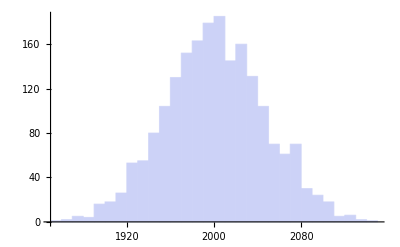

```mathematica
Histogram[(citedNumOfJournals=normDistBase[numOfJournals,1])]
```

何番目の雑誌から引用されるかはランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited]);
```

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]]);
```

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST]);
```

プロット

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Zipf Citation Model (実践的サイズ 2)

### model function

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

### application

雑誌数を2000に

```mathematica
numOfJournals=2000
```

2000

各雑誌の被引用数がzipfの法則に従うとする

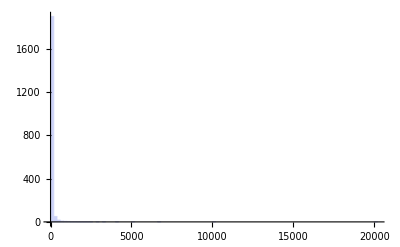

```mathematica
Histogram[(citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,1,10],{n,numOfJournals}]//N])]
```

```mathematica
citedNumOfJournals//Min
```

10

何番目の雑誌から引用されるかは一様にランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited]);
```

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]]);
```

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST]);
```

プロット

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## Zipf Citation Model (実践的サイズ 2)

### model function

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

### application

雑誌数を2000に

```mathematica
numOfJournals=2000
```

2000

各雑誌の被引用数がzipfの法則に従うとする

```mathematica
Histogram[(citedNumOfJournals=Ceiling[Table[numOfJournals*zipFF[n,1,10],{n,numOfJournals}]//N])]
```

-Graphics-

```mathematica
citedNumOfJournals//Min
```

10

何番目の雑誌から引用されるかは一様にランダムに決定

```mathematica
(journalCited=Table[RandomInteger[{1,numOfJournals},citedNumOfJournals[[n]]],{n,numOfJournals}]);
```

被引用引用行列(行が被引用ベクトル)を上記より作成

```mathematica
(linkageTable=journalCitedToMat[journalCited]);
```

被引用ベクトルを合計値(1)で正規化

```mathematica
(linkageTableST=standerdizeSum[N[linkageTable]]);
```

プロットのためPCA

```mathematica
(linkageTableSTPC=PrincipalComponents[linkageTableST]);
```

プロット

```mathematica
Graphics3D[{Map[Point[{#[[1]],#[[2]],#[[3]]}]&,linkageTableSTPC]}]
```

-Graphics3D-

## 引用誌の引用を偏らせる(Zipf;2000誌;変数を変化)

雑誌数を2000にする

```mathematica
numofjournals=2000
```

2000

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

aとcを変化

```mathematica
citedBase=.
```

```mathematica
Table[citedBase[a,c]=Round[Table[numofjournals zipFF[n,a,c],{n,numofjournals}]//N],{a,1,1.5,0.1},{c,1,7,1}];
```

各雑誌からの引用数を偏らせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はないとするので、被引用数をランダムに並べ替える

元となる被引用引用行列をつくる

```mathematica
citedcitingTab=.
```

```mathematica
Table[(citedcitingTab[a,c]=Table[citedBase[a,c][[randomOrder[numofjournals]]],{numofjournals}])//Dimensions,{a,1,1.5,0.1},{c,1,7,1}]
```

{{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}}}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
citedcitingNextMaxSelfTab=.
```

```mathematica
Table[(citedcitingNextMaxSelfTab[a,c]=nextMaxSelf[citedcitingTab[a,c]])//Dimensions,{a,1,1.5,0.1},{c,1,7,1}]
```

{{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}}}

合計値で正規化する

```mathematica
citedcitingNextMaxSelfTabST=.
```

```mathematica
Table[(citedcitingNextMaxSelfTabST[a,c]=standerdizeSum[citedcitingNextMaxSelfTab[a,c]]//N)//Dimensions,{a,1,1.5,0.1},{c,1,7,1}]
```

{{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}},{{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000},{2000,2000}}}

合計値が1になっていることの確認

```mathematica
Table[Map[Tr[#]&,citedcitingNextMaxSelfTabST[a,c]],{a,1,1.5,0.1},{c,1,7,1}]//Flatten//Chop//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=.
```

```mathematica
Table[citedcitingNextMaxSelfTabSTPCA[a,c]=PrincipalComponents[citedcitingNextMaxSelfTabST[a,c]],{a,1,1.5,0.1},{c,1,7,1}]//Dimensions
```

{{«1»},{«1»},«1»,«1»,{{{0.00204011,0.00277131,0.00709054,0.00164705,0.00147257,0.00260814,0.00348821,0.00229962,0.0105632,0.00573917,«1980»,7.66983×10^-6,0.0000675922,0.0000233569,0.0000280539,0.0000287767,5.30197×10^-6,1.76789×10^-6,6.8388×10^-7,7.1579×10^-7,0.},«1998»,{«1»}},«6»},{«1»}}

第1、2、3軸でプロット

```mathematica
exp1=.
```

```mathematica
Table[exp1[a,c]={Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA[a,c]]],a,c},{a,1,1.5,0.1},{c,1,7,1}]
```

{{{-Graphics3D-,1.,1},{-Graphics3D-,1.,2},{-Graphics3D-,1.,3},{-Graphics3D-,1.,4},{-Graphics3D-,1.,5},{-Graphics3D-,1.,6},{-Graphics3D-,1.,7}},{{-Graphics3D-,1.1,1},{-Graphics3D-,1.1,2},{-Graphics3D-,1.1,3},{-Graphics3D-,1.1,4},{-Graphics3D-,1.1,5},{-Graphics3D-,1.1,6},{-Graphics3D-,1.1,7}},{{-Graphics3D-,1.2,1},{-Graphics3D-,1.2,2},{-Graphics3D-,1.2,3},{-Graphics3D-,1.2,4},{-Graphics3D-,1.2,5},{-Graphics3D-,1.2,6},{-Graphics3D-,1.2,7}},{{-Graphics3D-,1.3,1},{-Graphics3D-,1.3,2},{-Graphics3D-,1.3,3},{-Graphics3D-,1.3,4},{-Graphics3D-,1.3,5},{-Graphics3D-,1.3,6},{-Graphics3D-,1.3,7}},{{-Graphics3D-,1.4,1},{-Graphics3D-,1.4,2},{-Graphics3D-,1.4,3},{-Graphics3D-,1.4,4},{-Graphics3D-,1.4,5},{-Graphics3D-,1.4,6},{-Graphics3D-,1.4,7}},{{-Graphics3D-,1.5,1},{-Graphics3D-,1.5,2},{-Graphics3D-,1.5,3},{-Graphics3D-,1.5,4},{-Graphics3D-,1.5,5},{-Graphics3D-,1.5,6},{-Graphics3D-,1.5,7}}}

## 引用誌の引用を偏らせる(Zipf;6000誌)

雑誌数を6000にする

```mathematica
numofjournals=6000
```

6000

Zipfの法則

```mathematica
zipFF[rank_,a_,c_]:=c rank^(-a)
```

Zipfの法則に従う被引用数を発生させる(最大の被引用数が600になるよう調整した)

```mathematica
citedBase=Round[Table[numofjournals zipFF[n,1,1]/10,{n,numofjournals}]//N];
```

```mathematica
citedBase[[1]]
```

600

ゼロのカウント

```mathematica
Count[citedBase,0]
```

4801

すべての雑誌において被引用数の合計値は4765になる

```mathematica
citedBase//Tr
```

4765

各雑誌からの引用数を偏らせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はないとするので、被引用数をランダムに並べ替える

元となる被引用引用行列をつくる

```mathematica
(citedcitingTab=Table[citedBase[[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{6000,6000}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//Dimensions
```

{6000,6000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)//Dimensions
```

{6000,6000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]//Chop//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

第10、11、12軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{10,11,12}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;ミニサイズ)

雑誌数を20にする

```mathematica
numofjournals=20
```

20

正規分布

```mathematica
Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N
```

{0.012703,0.0138992,0.0150569,0.0161486,0.0171472,0.0180263,0.018762,0.0193334,0.019724,0.0199222,0.0199222,0.019724,0.0193334,0.018762,0.0180263,0.0171472,0.0161486,0.0150569,0.0138992,0.012703}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
citedNumOfJournals=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]]
```

{16,16,20,20,30,23,26,17,22,20,18,20,18,21,20,20,18,26,17,26}

```mathematica
citedBase=citedNumOfJournals
```

{16,16,20,20,30,23,26,17,22,20,18,20,18,21,20,20,18,26,17,26}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
randomOrder[numofjournals]
```

{13,18,17,1,12,4,20,15,5,8,9,11,7,16,2,10,14,3,6,19}

```mathematica
citedBase[[randomOrder[numofjournals]]]
```

{22,20,30,23,18,26,18,17,20,20,21,18,20,26,16,20,17,16,20,26}

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab=Table[citedBase[[randomOrder[numofjournals]]],{numofjournals}])//TableForm
```

20 | 17 | 26 | 22 | 18 | 18 | 16 | 20 | 20 | 16 | 20 | 30 | 23 | 20 | 26 | 17 | 26 | 18 | 21 | 20
30 | 20 | 17 | 16 | 20 | 20 | 18 | 16 | 22 | 26 | 21 | 17 | 20 | 18 | 23 | 26 | 20 | 26 | 20 | 18
16 | 16 | 17 | 20 | 26 | 17 | 18 | 23 | 22 | 20 | 21 | 20 | 18 | 20 | 26 | 20 | 30 | 18 | 20 | 26
30 | 21 | 16 | 16 | 20 | 18 | 17 | 22 | 20 | 23 | 18 | 26 | 20 | 26 | 20 | 20 | 20 | 17 | 26 | 18
23 | 20 | 16 | 16 | 21 | 26 | 20 | 30 | 18 | 18 | 26 | 20 | 17 | 17 | 20 | 20 | 22 | 26 | 18 | 20
20 | 17 | 30 | 20 | 17 | 18 | 18 | 20 | 21 | 22 | 20 | 18 | 23 | 16 | 26 | 16 | 26 | 20 | 26 | 20
22 | 26 | 17 | 26 | 20 | 20 | 20 | 16 | 23 | 16 | 20 | 17 | 30 | 18 | 26 | 18 | 18 | 20 | 20 | 21
30 | 26 | 17 | 22 | 18 | 18 | 23 | 20 | 18 | 20 | 16 | 21 | 26 | 16 | 20 | 26 | 20 | 20 | 17 | 20
20 | 26 | 20 | 21 | 18 | 30 | 26 | 16 | 26 | 20 | 17 | 18 | 17 | 20 | 20 | 23 | 22 | 18 | 16 | 20
21 | 20 | 26 | 16 | 20 | 20 | 30 | 22 | 18 | 26 | 17 | 18 | 16 | 23 | 26 | 20 | 18 | 20 | 20 | 17
20 | 17 | 16 | 26 | 18 | 18 | 26 | 20 | 20 | 20 | 16 | 20 | 20 | 17 | 30 | 18 | 22 | 26 | 23 | 21
18 | 20 | 20 | 30 | 20 | 18 | 23 | 26 | 18 | 21 | 26 | 22 | 26 | 16 | 17 | 20 | 16 | 20 | 20 | 17
20 | 17 | 20 | 30 | 20 | 21 | 17 | 16 | 22 | 26 | 20 | 26 | 20 | 26 | 16 | 20 | 18 | 18 | 23 | 18
30 | 18 | 26 | 17 | 20 | 18 | 26 | 17 | 20 | 16 | 20 | 16 | 18 | 20 | 22 | 26 | 20 | 21 | 23 | 20
16 | 22 | 17 | 18 | 20 | 18 | 26 | 26 | 16 | 18 | 20 | 17 | 26 | 20 | 20 | 20 | 30 | 23 | 20 | 21
22 | 30 | 26 | 26 | 20 | 16 | 23 | 21 | 17 | 20 | 18 | 20 | 16 | 20 | 26 | 18 | 17 | 20 | 18 | 20
17 | 26 | 20 | 23 | 17 | 22 | 26 | 16 | 18 | 20 | 20 | 16 | 20 | 18 | 20 | 20 | 21 | 30 | 18 | 26
22 | 20 | 26 | 26 | 17 | 23 | 20 | 20 | 20 | 18 | 16 | 21 | 20 | 18 | 17 | 16 | 26 | 20 | 30 | 18
20 | 17 | 21 | 20 | 26 | 16 | 26 | 22 | 17 | 26 | 20 | 30 | 23 | 20 | 18 | 20 | 20 | 18 | 18 | 16
20 | 20 | 21 | 17 | 26 | 18 | 16 | 23 | 20 | 20 | 20 | 20 | 16 | 30 | 18 | 26 | 26 | 22 | 18 | 17

```mathematica
Map[Tr[#]&,citedcitingTab]
```

{414,414,414,414,414,414,414,414,414,414,414,414,414,414,414,414,414,414,414,414}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//TableForm
```

20 | 17 | 26 | 22 | 18 | 18 | 16 | 20 | 20 | 16 | 20 | 30 | 23 | 20 | 26 | 17 | 26 | 18 | 21 | 20
30 | 20 | 17 | 16 | 20 | 20 | 18 | 16 | 22 | 26 | 21 | 17 | 20 | 18 | 23 | 26 | 20 | 26 | 20 | 18
16 | 16 | 17 | 20 | 26 | 17 | 18 | 23 | 22 | 20 | 21 | 20 | 18 | 20 | 26 | 20 | 30 | 18 | 20 | 26
30 | 21 | 16 | 16 | 20 | 18 | 17 | 22 | 20 | 23 | 18 | 26 | 20 | 26 | 20 | 20 | 20 | 17 | 26 | 18
23 | 20 | 16 | 16 | 21 | 26 | 20 | 30 | 18 | 18 | 26 | 20 | 17 | 17 | 20 | 20 | 22 | 26 | 18 | 20
20 | 17 | 30 | 20 | 17 | 18 | 18 | 20 | 21 | 22 | 20 | 18 | 23 | 16 | 26 | 16 | 26 | 20 | 26 | 20
22 | 26 | 17 | 26 | 20 | 20 | 20 | 16 | 23 | 16 | 20 | 17 | 30 | 18 | 26 | 18 | 18 | 20 | 20 | 21
30 | 26 | 17 | 22 | 18 | 18 | 23 | 20 | 18 | 20 | 16 | 21 | 26 | 16 | 20 | 26 | 20 | 20 | 17 | 20
20 | 26 | 20 | 21 | 18 | 30 | 26 | 16 | 26 | 20 | 17 | 18 | 17 | 20 | 20 | 23 | 22 | 18 | 16 | 20
21 | 20 | 26 | 16 | 20 | 20 | 30 | 22 | 18 | 26 | 17 | 18 | 16 | 23 | 26 | 20 | 18 | 20 | 20 | 17
20 | 17 | 16 | 26 | 18 | 18 | 26 | 20 | 20 | 20 | 16 | 20 | 20 | 17 | 30 | 18 | 22 | 26 | 23 | 21
18 | 20 | 20 | 30 | 20 | 18 | 23 | 26 | 18 | 21 | 26 | 22 | 26 | 16 | 17 | 20 | 16 | 20 | 20 | 17
20 | 17 | 20 | 30 | 20 | 21 | 17 | 16 | 22 | 26 | 20 | 26 | 20 | 26 | 16 | 20 | 18 | 18 | 23 | 18
30 | 18 | 26 | 17 | 20 | 18 | 26 | 17 | 20 | 16 | 20 | 16 | 18 | 20 | 22 | 26 | 20 | 21 | 23 | 20
16 | 22 | 17 | 18 | 20 | 18 | 26 | 26 | 16 | 18 | 20 | 17 | 26 | 20 | 20 | 20 | 30 | 23 | 20 | 21
22 | 30 | 26 | 26 | 20 | 16 | 23 | 21 | 17 | 20 | 18 | 20 | 16 | 20 | 26 | 18 | 17 | 20 | 18 | 20
17 | 26 | 20 | 23 | 17 | 22 | 26 | 16 | 18 | 20 | 20 | 16 | 20 | 18 | 20 | 20 | 21 | 30 | 18 | 26
22 | 20 | 26 | 26 | 17 | 23 | 20 | 20 | 20 | 18 | 16 | 21 | 20 | 18 | 17 | 16 | 26 | 20 | 30 | 18
20 | 17 | 21 | 20 | 26 | 16 | 26 | 22 | 17 | 26 | 20 | 30 | 23 | 20 | 18 | 20 | 20 | 18 | 18 | 16
20 | 20 | 21 | 17 | 26 | 18 | 16 | 23 | 20 | 20 | 20 | 20 | 16 | 30 | 18 | 26 | 26 | 22 | 18 | 17

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)
```

{{0.0483092,0.0410628,0.0628019,0.0531401,0.0434783,0.0434783,0.0386473,0.0483092,0.0483092,0.0386473,0.0483092,0.0724638,0.0555556,0.0483092,0.0628019,0.0410628,0.0628019,0.0434783,0.0507246,0.0483092},{0.0724638,0.0483092,0.0410628,0.0386473,0.0483092,0.0483092,0.0434783,0.0386473,0.0531401,0.0628019,0.0507246,0.0410628,0.0483092,0.0434783,0.0555556,0.0628019,0.0483092,0.0628019,0.0483092,0.0434783},{0.0386473,0.0386473,0.0410628,0.0483092,0.0628019,0.0410628,0.0434783,0.0555556,0.0531401,0.0483092,0.0507246,0.0483092,0.0434783,0.0483092,0.0628019,0.0483092,0.0724638,0.0434783,0.0483092,0.0628019},{0.0724638,0.0507246,0.0386473,0.0386473,0.0483092,0.0434783,0.0410628,0.0531401,0.0483092,0.0555556,0.0434783,0.0628019,0.0483092,0.0628019,0.0483092,0.0483092,0.0483092,0.0410628,0.0628019,0.0434783},{0.0555556,0.0483092,0.0386473,0.0386473,0.0507246,0.0628019,0.0483092,0.0724638,0.0434783,0.0434783,0.0628019,0.0483092,0.0410628,0.0410628,0.0483092,0.0483092,0.0531401,0.0628019,0.0434783,0.0483092},{0.0483092,0.0410628,0.0724638,0.0483092,0.0410628,0.0434783,0.0434783,0.0483092,0.0507246,0.0531401,0.0483092,0.0434783,0.0555556,0.0386473,0.0628019,0.0386473,0.0628019,0.0483092,0.0628019,0.0483092},{0.0531401,0.0628019,0.0410628,0.0628019,0.0483092,0.0483092,0.0483092,0.0386473,0.0555556,0.0386473,0.0483092,0.0410628,0.0724638,0.0434783,0.0628019,0.0434783,0.0434783,0.0483092,0.0483092,0.0507246},{0.0724638,0.0628019,0.0410628,0.0531401,0.0434783,0.0434783,0.0555556,0.0483092,0.0434783,0.0483092,0.0386473,0.0507246,0.0628019,0.0386473,0.0483092,0.0628019,0.0483092,0.0483092,0.0410628,0.0483092},{0.0483092,0.0628019,0.0483092,0.0507246,0.0434783,0.0724638,0.0628019,0.0386473,0.0628019,0.0483092,0.0410628,0.0434783,0.0410628,0.0483092,0.0483092,0.0555556,0.0531401,0.0434783,0.0386473,0.0483092},{0.0507246,0.0483092,0.0628019,0.0386473,0.0483092,0.0483092,0.0724638,0.0531401,0.0434783,0.0628019,0.0410628,0.0434783,0.0386473,0.0555556,0.0628019,0.0483092,0.0434783,0.0483092,0.0483092,0.0410628},{0.0483092,0.0410628,0.0386473,0.0628019,0.0434783,0.0434783,0.0628019,0.0483092,0.0483092,0.0483092,0.0386473,0.0483092,0.0483092,0.0410628,0.0724638,0.0434783,0.0531401,0.0628019,0.0555556,0.0507246},{0.0434783,0.0483092,0.0483092,0.0724638,0.0483092,0.0434783,0.0555556,0.0628019,0.0434783,0.0507246,0.0628019,0.0531401,0.0628019,0.0386473,0.0410628,0.0483092,0.0386473,0.0483092,0.0483092,0.0410628},{0.0483092,0.0410628,0.0483092,0.0724638,0.0483092,0.0507246,0.0410628,0.0386473,0.0531401,0.0628019,0.0483092,0.0628019,0.0483092,0.0628019,0.0386473,0.0483092,0.0434783,0.0434783,0.0555556,0.0434783},{0.0724638,0.0434783,0.0628019,0.0410628,0.0483092,0.0434783,0.0628019,0.0410628,0.0483092,0.0386473,0.0483092,0.0386473,0.0434783,0.0483092,0.0531401,0.0628019,0.0483092,0.0507246,0.0555556,0.0483092},{0.0386473,0.0531401,0.0410628,0.0434783,0.0483092,0.0434783,0.0628019,0.0628019,0.0386473,0.0434783,0.0483092,0.0410628,0.0628019,0.0483092,0.0483092,0.0483092,0.0724638,0.0555556,0.0483092,0.0507246},{0.0531401,0.0724638,0.0628019,0.0628019,0.0483092,0.0386473,0.0555556,0.0507246,0.0410628,0.0483092,0.0434783,0.0483092,0.0386473,0.0483092,0.0628019,0.0434783,0.0410628,0.0483092,0.0434783,0.0483092},{0.0410628,0.0628019,0.0483092,0.0555556,0.0410628,0.0531401,0.0628019,0.0386473,0.0434783,0.0483092,0.0483092,0.0386473,0.0483092,0.0434783,0.0483092,0.0483092,0.0507246,0.0724638,0.0434783,0.0628019},{0.0531401,0.0483092,0.0628019,0.0628019,0.0410628,0.0555556,0.0483092,0.0483092,0.0483092,0.0434783,0.0386473,0.0507246,0.0483092,0.0434783,0.0410628,0.0386473,0.0628019,0.0483092,0.0724638,0.0434783},{0.0483092,0.0410628,0.0507246,0.0483092,0.0628019,0.0386473,0.0628019,0.0531401,0.0410628,0.0628019,0.0483092,0.0724638,0.0555556,0.0483092,0.0434783,0.0483092,0.0483092,0.0434783,0.0434783,0.0386473},{0.0483092,0.0483092,0.0507246,0.0410628,0.0628019,0.0434783,0.0386473,0.0555556,0.0483092,0.0483092,0.0483092,0.0483092,0.0386473,0.0724638,0.0434783,0.0628019,0.0628019,0.0531401,0.0434783,0.0410628}}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;2000誌)

雑誌数を2000にする

```mathematica
numofjournals=2000
```

2000

正規分布

```mathematica
Table[PDF[NormalDistribution[2000,2000],x],{x,1,39,2}]//N
```

{0.000121046,0.000121167,0.000121288,0.000121409,0.00012153,0.000121651,0.000121772,0.000121893,0.000122014,0.000122135,0.000122256,0.000122377,0.000122498,0.000122619,0.00012274,0.00012286,0.000122981,0.000123102,0.000123223,0.000123344}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
citedNumOfJournals=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]];
```

```mathematica
citedBase=citedNumOfJournals;
```

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab=Table[citedBase[[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{2000,2000}

```mathematica
Map[Tr[#]&,citedcitingTab]//Union
```

{4002596}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//Dimensions
```

{2000,2000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)//Dimensions
```

{2000,2000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Table[0,{20}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Graphics3D[{Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA],RGBColor[1,0,0],PointSize[0.05],Point[Table[0,{3}]]}]
```

-Graphics3D-

第1、2軸平面における第1軸からのコサイン距離(unshiftなし)

```mathematica
(cosdistlist[1]=Map[CosineDistance[#[[{1,2}]],{1,0}]&,citedcitingNextMaxSelfTabSTPCA])//Dimensions
```

{2000}

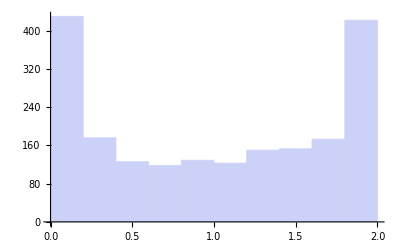

```mathematica
Histogram[cosdistlist[1]]
```

## 引用誌の引用を偏らせる(正規分布,一回のみ発生;6000誌)

雑誌数を2000にする

```mathematica
numofjournals=6000
```

6000

正規分布

```mathematica
Table[PDF[NormalDistribution[6000,6000],x],{x,1,39,2}]//N
```

{0.0000403352,0.0000403486,0.0000403621,0.0000403755,0.0000403889,0.0000404024,0.0000404158,0.0000404293,0.0000404427,0.0000404562,0.0000404696,0.000040483,0.0000404965,0.0000405099,0.0000405234,0.0000405368,0.0000405503,0.0000405637,0.0000405771,0.0000405906}

各雑誌からの引用数正規分布に従わせる(全ての雑誌において被引用数のパターンは同じ)。どの雑誌から引用されるかは、各誌とも一様ランダムで重複はない

```mathematica
(*(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length*)
```

```mathematica
(citedNumOfJournals=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]])//Length
```

6000

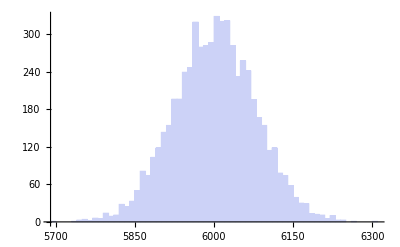

```mathematica
Histogram[citedNumOfJournals]
```

```mathematica
citedBase=citedNumOfJournals;
```

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab=Table[citedBase[[randomOrder[numofjournals]]],{numofjournals}])//Dimensions
```

{6000,6000}

```mathematica
Map[Tr[#]&,citedcitingTab]//Union
```

{36007054}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//Dimensions
```

{6000,6000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)//Dimensions
```

{6000,6000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]//Chop//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット、スパイクは見えない

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

## 引用誌の引用を偏らせる(正規分布,分散小;ミニサイズ)

雑誌数を20にする

```mathematica
numofjournals=20
```

20

正規分布

```mathematica
(citedNumOfJournals=Ceiling[1000Table[PDF[NormalDistribution[20,20],x],{x,1,39,2}]//N])//Length
```

20

```mathematica
citedNumOfJournals=Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]]
```

{20,24,19,19,13,15,20,21,20,30,23,21,18,18,25,23,18,19,24,25}

```mathematica
citedBase=citedNumOfJournals
```

{20,24,19,19,13,15,20,21,20,30,23,21,18,18,25,23,18,19,24,25}

どの雑誌から引用されるかは、一様ランダムで重複がないとするので、オーダーをランダムにする(つまり各誌からの被引用数をランダムに並べ替える)

```mathematica
randomOrder[numofjournals]
```

{7,1,10,20,13,6,17,2,18,9,3,14,19,4,11,16,15,5,12,8}

ランダムに並べ替えられた基となる被引用引用行列

```mathematica
(citedcitingTab=Table[citedBase[[randomOrder[numofjournals]]],{numofjournals}])//TableForm
```

25 | 19 | 19 | 13 | 24 | 23 | 19 | 18 | 18 | 20 | 24 | 20 | 20 | 21 | 21 | 25 | 23 | 15 | 30 | 18
20 | 19 | 23 | 20 | 25 | 24 | 13 | 30 | 23 | 18 | 18 | 21 | 19 | 21 | 20 | 19 | 15 | 24 | 25 | 18
18 | 15 | 24 | 19 | 20 | 20 | 21 | 23 | 20 | 25 | 13 | 21 | 24 | 18 | 18 | 19 | 30 | 23 | 19 | 25
19 | 20 | 20 | 23 | 13 | 20 | 18 | 19 | 25 | 24 | 30 | 19 | 21 | 18 | 24 | 25 | 15 | 23 | 21 | 18
15 | 21 | 24 | 23 | 25 | 30 | 21 | 18 | 20 | 24 | 19 | 13 | 20 | 18 | 23 | 19 | 20 | 25 | 18 | 19
24 | 21 | 19 | 15 | 18 | 20 | 30 | 25 | 21 | 25 | 24 | 23 | 20 | 20 | 19 | 19 | 13 | 18 | 18 | 23
18 | 19 | 20 | 23 | 21 | 24 | 25 | 24 | 15 | 13 | 21 | 19 | 20 | 30 | 18 | 23 | 18 | 25 | 19 | 20
23 | 18 | 19 | 18 | 20 | 20 | 24 | 25 | 21 | 19 | 21 | 19 | 20 | 15 | 13 | 30 | 25 | 23 | 18 | 24
30 | 18 | 25 | 25 | 20 | 21 | 19 | 24 | 20 | 23 | 21 | 18 | 20 | 13 | 18 | 15 | 24 | 19 | 19 | 23
24 | 15 | 18 | 21 | 13 | 19 | 20 | 24 | 18 | 19 | 20 | 23 | 21 | 20 | 30 | 19 | 25 | 23 | 25 | 18
21 | 24 | 25 | 23 | 18 | 13 | 20 | 19 | 24 | 20 | 19 | 19 | 30 | 21 | 23 | 15 | 20 | 18 | 25 | 18
23 | 18 | 19 | 25 | 19 | 18 | 20 | 24 | 24 | 25 | 13 | 15 | 21 | 20 | 20 | 30 | 19 | 21 | 18 | 23
21 | 21 | 18 | 24 | 18 | 30 | 19 | 15 | 20 | 23 | 24 | 19 | 18 | 25 | 20 | 25 | 23 | 13 | 20 | 19
15 | 19 | 20 | 19 | 23 | 24 | 13 | 18 | 21 | 20 | 23 | 18 | 19 | 20 | 25 | 24 | 21 | 30 | 25 | 18
24 | 24 | 18 | 21 | 20 | 19 | 15 | 23 | 30 | 25 | 13 | 20 | 18 | 21 | 18 | 23 | 19 | 25 | 20 | 19
18 | 24 | 23 | 19 | 20 | 18 | 13 | 24 | 15 | 21 | 20 | 19 | 20 | 18 | 19 | 25 | 25 | 30 | 21 | 23
19 | 20 | 23 | 15 | 19 | 19 | 18 | 18 | 25 | 24 | 30 | 25 | 21 | 21 | 20 | 18 | 24 | 13 | 20 | 23
23 | 18 | 21 | 21 | 18 | 19 | 19 | 13 | 19 | 25 | 20 | 30 | 23 | 20 | 20 | 25 | 24 | 24 | 18 | 15
25 | 19 | 19 | 24 | 24 | 20 | 20 | 19 | 18 | 23 | 18 | 18 | 23 | 13 | 21 | 20 | 15 | 21 | 30 | 25
19 | 25 | 18 | 24 | 21 | 20 | 18 | 19 | 19 | 23 | 20 | 30 | 25 | 15 | 18 | 20 | 24 | 13 | 23 | 21

```mathematica
Map[Tr[#]&,citedcitingTab]
```

{415,415,415,415,415,415,415,415,415,415,415,415,415,415,415,415,415,415,415,415}

## 引用誌の引用を偏らせる(正規分布,毎回発生,分散小;2000誌)

雑誌数を20にする

```mathematica
numofjournals=2000
```

2000

正規分布: 平均2000,分散√2000

```mathematica
Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]]
```

{1907,2020,2105,1981,2077,2015,2021,1959,1988,2006,1969,2000,2064,1972,1976,2088,2031,2051,1996,1984,2025,2036,1932,1980,2023,1985,1963,1978,1967,1984,1954,1966,1964,1978,2048,2020,1963,2016,2012,2042,1961,2020,2005,1901,1951,2028,1934,1999,1984,2052,2013,2039,2048,1970,1958,2029,1969,1991,2010,2014,1990,2024,1992,2046,1948,1954,2018,1965,1944,2021,2016,2023,2095,2007,2039,1936,1931,2007,2049,1954,2051,1966,1910,2076,2043,1960,2040,2055,2049,1994,1988,1994,1944,1998,2051,1975,1942,1968,1980,1960,2000,2005,1980,2030,1983,1940,2053,1958,1994,1940,2028,1975,1966,2006,1999,2003,2044,2037,2026,1959,1952,2027,1935,1998,2130,2028,2002,2125,1990,2032,1926,2033,1926,1969,2017,1953,1929,2018,2071,1988,2048,2014,2010,1925,1971,2015,2000,2007,2028,1954,1982,1993,2017,1997,2018,1887,1953,1983,2097,2045,2103,2026,2025,2054,2078,2005,1984,1992,1925,2037,2016,2028,2012,2076,1989,2032,2026,2026,1925,2065,1988,2048,2028,1979,1946,1971,2003,2027,1939,2035,1982,2059,2046,1998,2008,2018,1985,1972,2020,2006,1984,2030,2023,1967,1943,1931,2066,2036,2034,1940,1941,2029,2060,1985,2020,2061,2035,2056,1952,2012,1996,1970,1964,1976,1939,1990,1923,2041,2061,2020,2055,2027,1981,2026,1941,1924,1945,2012,2013,1999,1969,2033,2001,2052,1965,2013,1966,1944,1951,2042,2064,2023,2096,2019,1953,2103,1997,1935,1974,2081,1959,2021,2060,1953,2047,1986,1982,1893,2078,1975,2110,1995,1954,1978,2074,2127,2045,1974,2017,1966,1932,2019,1947,1955,1951,2009,2007,2035,1971,1995,1960,2010,2087,2030,2027,2012,1973,2041,2006,1962,1926,1976,1973,1858,1990,1965,1991,2039,1976,1954,1995,2043,1988,2010,1981,2067,1909,1988,1954,1983,2015,2001,1948,1993,2005,1981,1986,1953,2019,1944,2028,1981,1989,2008,1996,2005,1935,1992,2009,1992,1985,2003,1959,1970,1984,2016,2006,1997,2073,2002,1979,1989,2089,1978,2023,1913,1978,1943,2019,1962,1944,1973,2004,1977,2042,2028,1981,2051,2011,1922,1955,1952,1969,1963,2050,1973,2002,1952,2078,1997,2065,1988,2007,2004,2040,1998,2004,1963,2036,2005,1959,1942,2005,1967,2006,2061,1969,1935,2092,2026,1996,2011,1917,2022,2053,1993,1999,2010,1999,1993,1979,2039,2018,2002,2009,2006,1932,1977,1982,2056,1993,1958,1958,2069,2004,2008,2024,2005,2019,1971,2028,2031,2003,2012,1939,1963,2033,1979,1944,2000,1996,1946,1945,2022,2013,1956,2064,2018,1966,2044,1915,2012,1966,1896,2070,1945,2035,2006,2028,2033,2066,2050,1932,2011,2005,2014,2080,2048,2011,2071,1950,1978,1987,1953,1956,1996,1997,1952,1898,1955,1940,1981,1954,2054,1983,1998,1994,1978,1986,1968,2050,1939,1997,2048,2053,2030,2030,1983,1996,1959,2012,1983,1876,2018,1987,1969,2002,1984,1981,2012,2029,2000,1984,1944,2023,1935,2006,2062,1994,1989,1975,2029,2020,2019,1979,2000,2105,1938,1916,1970,2083,2039,1990,2012,2027,1947,1977,1947,1988,2008,1982,1995,2010,2104,2021,1968,1894,2008,2008,1990,2003,2005,1956,1956,1958,1945,1938,2014,1936,2062,2019,1968,1981,1997,1991,2007,2050,1952,2018,1974,2046,1995,2039,2035,2102,2010,2011,1861,2016,2045,1981,2031,1972,1980,2012,2030,1968,1960,2032,1942,1980,2058,1996,1990,1987,2060,2010,1985,1991,1969,2002,2007,1969,2002,2021,1924,2002,1963,2005,2051,1997,1998,2005,1945,1993,1990,1985,2062,1894,2104,2079,1988,1918,2011,2039,1968,2037,2044,1977,1936,1998,1980,1952,2100,1956,1981,1990,1922,2004,1983,2037,2077,2058,2009,2073,1949,2062,1976,1962,1940,2003,2039,1903,2049,2023,2116,2002,1995,1949,1968,1964,1989,2064,2074,2017,1980,1961,2031,2064,2067,1964,2060,1961,2023,2053,1978,1942,2050,1997,1985,1943,2035,1891,2039,2080,2035,1956,1998,2039,1976,1933,1960,2063,1981,1986,2031,1965,2001,1985,2014,2022,2021,2053,2035,2003,2000,2019,2021,2012,2018,1965,1950,2002,1957,2017,2020,1996,1939,2033,1949,2087,1985,1999,1972,1973,2014,2046,1995,1931,1987,1977,1973,2010,2074,1991,1978,2015,2000,1977,2016,1955,1981,1947,1981,2059,1975,1957,1965,2021,1948,1966,1974,2019,2072,2053,2051,2043,1966,2047,1995,2011,1989,1989,2086,1971,2037,1967,2026,2057,1928,1991,1952,1914,1959,1983,2028,2085,1967,2117,1964,2071,1993,1996,2006,1968,1950,2022,2026,2013,1916,2017,2009,1966,1967,1999,2051,2001,1908,1995,1940,2005,2073,1959,2038,1950,1959,2010,1993,1987,2068,2082,1971,1989,2023,2010,2064,2060,2011,1971,1983,2003,1961,2059,2056,1962,2030,2025,1981,2064,2008,2043,2008,2006,1979,1927,2046,2064,1942,1969,2039,2080,1982,1952,2044,2037,2017,1959,2018,2004,1988,2054,2027,1904,1937,2085,1957,1993,1966,2016,2011,1982,1966,2030,1893,1995,2002,1999,2032,2012,2025,1965,2089,1994,2034,1960,1962,2045,2032,1974,2016,1982,1919,1991,2053,1887,1967,2081,1962,1980,2072,1966,1990,2034,2019,2025,1985,1916,1998,2016,2018,2010,1984,2021,1986,2024,1990,1931,1966,1982,2065,1987,1958,1970,2014,1994,2044,2039,1968,1970,1967,2038,2036,1936,1944,1985,1981,1938,1955,1970,1964,2045,1970,2022,1982,2000,2027,1933,2047,1982,1993,1956,1957,2082,2059,2010,2027,2014,2032,2019,2121,2077,2035,2037,1891,1899,1974,1941,2051,2019,1988,1939,2033,1988,2043,2037,2002,1923,2041,2038,1997,2008,2056,2083,2023,1990,1998,1988,1967,2008,1958,2003,1962,1951,2037,2054,1953,2052,2004,1981,2019,2057,1955,1965,1942,2018,2049,1964,2008,2000,1946,1935,1941,1971,1927,1865,1908,1972,1990,2076,2007,1966,2007,2045,2020,2003,1971,2099,2031,2012,2062,1983,1969,1959,2010,2002,1998,2000,2034,1991,2090,1985,2028,2029,1957,1938,2060,2009,2017,1887,2023,2032,1978,2081,2040,1951,2061,2011,2004,2038,2106,1957,1931,1991,1973,2006,1959,2034,1987,1999,2015,2026,1961,2019,1980,2017,1965,1960,1981,2023,2087,1987,1968,2158,1960,2039,2042,2060,2050,1955,2042,1961,2000,2031,2057,2046,2042,2036,2051,2028,2062,2015,1986,2011,2043,2004,1979,1989,1946,1960,2021,2054,2018,2030,2018,1951,1978,2049,1978,1980,2094,2009,1970,1965,2000,2058,1954,1985,2017,1961,1942,2024,2056,1984,2077,1997,2025,1962,1991,1941,1894,2027,1991,2038,2047,2057,2034,2046,2098,2015,1977,1981,2039,2031,1963,2114,2044,2071,1992,2060,2004,1965,2013,1975,2029,1992,1988,1919,1984,2050,2070,1905,2067,1956,2022,1962,1930,2037,1972,1967,2082,2000,2004,2011,2006,2002,2047,2049,1982,1927,2077,1923,2068,2060,2007,1979,2076,1950,1925,1964,2046,1928,1965,1980,2019,2021,2013,1951,2008,2093,1941,2045,2070,1949,2014,2034,2001,2097,1907,2015,1901,1946,1999,2014,2079,1890,2089,1929,2040,1980,1991,2019,1940,1992,2021,2063,2082,1972,2068,1959,2005,1978,1971,1984,2000,1989,2052,1993,1896,2033,2029,2022,2009,1939,1905,1961,1941,1930,1974,1950,2092,2005,1957,1938,2003,2026,1936,2023,2013,1895,2034,1978,2020,2033,2083,2008,1976,1954,2046,1990,2038,2036,2012,2036,2016,2023,1988,2000,1980,2079,1993,2046,2038,1927,2054,1980,2033,1968,2084,2029,2107,1985,1979,2030,2041,1930,2044,1943,1989,1945,2096,1963,1986,2071,2077,1987,2039,1978,2040,2011,1975,2008,2048,2017,2048,2054,2029,1971,2033,2049,1985,1918,2083,2023,1969,1988,2060,1939,1958,2041,1975,2027,1938,2011,2013,1921,2010,2061,1983,2014,2003,1960,1960,1989,1992,2062,2003,2017,2015,2069,2046,1970,2011,2056,2025,1983,2041,1949,1987,2040,2016,2004,2008,2049,1994,2061,1976,1992,1980,1966,1937,1935,2002,1921,2044,2042,1987,2012,2126,1996,1905,2081,2024,1977,1928,1985,1980,2031,1911,1974,2020,2019,1953,2017,1978,2020,1960,1967,2001,2030,1976,1987,2013,2018,2059,2022,2011,1965,1968,2054,1999,2023,2015,1996,2018,2027,1981,1941,2066,1994,2023,2024,1978,2117,2010,2050,2060,1961,2006,2001,2014,1961,1996,2059,2011,1964,2037,2037,1960,1968,1996,1995,2081,1969,1979,1988,2074,1970,2039,2010,2027,2065,2043,1997,2089,1958,2027,2020,2018,2047,2021,2106,1987,2054,1966,2001,2006,1967,2056,2006,1979,1988,2030,2064,1950,2032,1994,2034,2022,1977,2085,2006,2080,1947,2074,2002,1995,1902,1988,2005,2045,2017,2052,1976,2015,2056,1964,2035,1976,2000,2076,2005,1946,2038,2011,1962,1939,1981,1996,2017,1991,2006,2023,2011,2027,2017,1971,1951,1996,2014,2004,2008,2012,1931,2021,1967,2016,2014,1989,2005,2035,2000,2007,1921,1899,2026,1942,1985,2064,2014,1989,1992,1975,1938,2027,1986,1928,2006,1994,1979,1967,2019,1954,2049,2043,1959,1977,1938,2049,2044,1939,2048,1945,1962,1919,1951,1996,1969,2014,1984,2030,2046,1944,1947,1884,1946,2103,2035,1949,2023,2002,2063,1910,1991,2008,2096,2009,1980,1992,2062,2079,2031,1991,1937,1942,2023,2023,2009,2039,2038,2003,2036,2048,2042,1957,1988,2009,2078,2060,1942,1922,1983,2001,1982,1943,1968,2026,2016,2033,2023,2006,2106,1915,1965,2069,1959,2038,1977,1958,1990,1955,1997,1969,2000,1958,2000,1962,2004,2041,1995,1945,2012,1980,2037,1962,1967,1936,2007,2036,2014,1987,2030,1990,1979,1974,2036,2019,1993,1917,2019,1944,2022,1950,2010,2053,2042,1930,1990,1978,2013,1986,2043,1968,2055,2080,1986,1988,2034,2029,1997,2022,1986,1968,1965,1921,1970,1904,2025,2004,1933,2039,1988,2021,2036,2032,2003,2049,2021,1941,1989,1970,1981,2008,2033,2015,1976,2005,1989,2065,1996,2022,1965,2075,1986,1988,2015,2056,2007,1968,2033,1992,1946,1980,1923,2085,2003,1959,2048,2046,2043,2018,2021,1968,2061,1983,1959,2021,1993,2051,2087,1960,2106,2061,1964,1948,2045,1952,2038,2064,2021,2074,2121,1961,1937,2003,2038,2019,2014,2012,1980,2102,1932,1972,1958,2008,2036,2018,2011,1971,2058,2018,1962,1990,1915,1980,2036,2036,1894,2015,2007,2051,2011,2057,2029,1958,2030,2070,1999,1957,1961,1946,2061,1996,2040,2005,1931,2075,1999,2029,1942,1903,2070,1997,2001,1974,2015,1971,2106,1954,2000,1944,2092,1996,2070,1951,1997,2023,1988,1981,1893,1969,1989,1989,2010,2060,2025,1943,2001,1981,1993,1957,2034,1988,1948,1960,2015,1969,2035,2039,2051,2031,2016,2030,1946,2033,1978,1917,1950,1991,1982,2016,1880,2013,2006,1881,1966,1990,2012,2033,2030,2007,1917,2046,1962,2015,2038,2064,2004,1993,1987,1980,1999,2075,2061,2045,1983,1927,2008,1961,1923,1987,1962,1908,2066,2055,1971,2055,1934,2000,1943,2005,1919,1952,2042,2002,1974,1928,1944,1962,1941,1951,1945,1941,2067,2051,1984,1972,2019,1990,2059,2101,2001,1979,1995,1985,2004,1992,2081,1968,1941,2032,1946,1976,2042,1924,1987,1897,1974,2024,2041,2021,2044,2018,1996,1967,1981,2019,2033,2032,2032,2062,2039,2023,2075,1945,1977,1956,2001,1974,1941,2055,2069,2013,1994,2019,2042,2007,2044,1983,2013,1972,1912,2012,2047,2059,1987,2037,2032,2104,2037,2008,2006,1989,1972,2057,1948,1985,1992,2002,2023,2043,1925,2022,1990,2125,2018,1981,2032,1993,2030,1946,1996,1971,2016,1995,2032,2047,2008,2027,2029,1983}

上記のベクトルを雑誌ごとに発生させ、被引用引用行列とする

```mathematica
(citedcitingTab=Table[Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]],{numofjournals}])//Dimensions
```

{2000,2000}

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//Dimensions
```

{2000,2000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)//Dimensions
```

{2000,2000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]//Chop//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

## 引用誌の引用を偏らせる(正規分布,毎回発生,分散大;2000誌)

雑誌数を20にする

```mathematica
numofjournals=2000
```

2000

正規分布: 平均2000,分散2000(0未満は0に)

```mathematica
Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,numofjournals],numofjournals]]]
```

{272,3981,0,2443,3145,2787,2441,2480,3996,3219,1673,2754,0,1947,4540,2791,4132,2332,122,1546,1486,693,0,2586,424,4507,5011,1327,3131,435,2551,6114,0,0,0,0,3035,837,5753,0,2612,0,1299,0,3296,0,434,5763,1324,2177,2082,3513,0,1203,1074,5027,4275,554,1236,1157,0,487,0,714,818,2632,0,4264,1503,2269,741,3261,3017,1168,4619,937,431,172,2354,420,0,3710,2791,2892,0,816,2,1356,126,0,2323,3459,1100,0,3999,3324,824,303,3079,498,1145,485,3634,0,1617,3781,435,1251,2649,3748,982,2824,2429,4000,1587,4573,2410,3969,1699,1745,1130,2002,0,360,3278,0,77,6443,1580,0,4561,2782,0,1936,3084,3979,0,1520,4275,3623,3289,4440,4376,1343,4371,2939,2155,3265,2458,3998,3750,3317,5224,1956,1333,3165,1025,0,6199,2006,3102,1999,4513,0,0,2900,1726,1883,2227,2889,2371,1332,1520,1716,3729,5115,1710,788,1030,2567,6451,1176,3558,2796,1451,7662,1567,1349,4196,223,1596,1621,483,0,999,3365,4004,2677,2951,1786,2756,2154,2796,2689,2483,2671,4191,7744,3955,1408,4209,4943,1565,2925,391,3538,6679,1231,571,4559,0,3173,0,0,1620,3676,2026,2649,0,0,740,0,2487,7358,2838,3241,3895,1294,4693,3610,0,2436,1918,3122,5751,301,0,2244,3006,0,979,1394,2420,2262,2561,3089,3344,3171,1545,2443,2583,632,255,563,4434,4194,50,0,2409,2957,1184,3479,2461,769,213,509,2955,2776,3867,0,1056,1818,2044,0,3952,3085,1373,3622,0,3066,972,1224,392,2044,565,0,2261,5552,3949,2241,727,0,208,1240,4562,2534,3850,2776,4967,5091,3094,726,1384,0,0,3391,2090,412,3905,493,2306,0,2040,0,0,2404,486,1701,1691,3339,0,1689,155,5450,1251,3317,4799,779,1481,4717,2750,5024,2879,1924,5192,2776,0,2221,480,683,3557,2459,1820,1707,0,0,0,1058,472,2428,0,2184,1194,1651,1866,2934,3930,4365,7179,2225,852,6384,419,732,0,4846,1387,399,2359,303,512,2786,3822,2522,3035,380,843,1786,5321,0,2191,1579,0,42,3070,3610,2712,358,3846,2012,1609,1567,1083,2098,4313,5041,5804,1096,0,3890,0,3844,2839,252,1280,215,2089,4346,2549,2419,2652,1263,0,1627,6585,2296,5243,2456,850,1398,3652,0,1046,2477,6487,2601,0,0,1030,4153,0,0,2170,465,1482,0,790,0,3713,816,1306,2076,3682,2866,1284,4854,4493,2296,3515,2188,3953,3447,4981,1222,1270,2368,4405,1685,6747,1688,1577,1482,1662,260,3958,0,904,1607,3526,2007,2614,1457,2765,1413,2522,2955,369,0,964,2112,0,3556,1028,4968,6566,211,3483,1329,2869,4344,1732,1382,4124,1079,2548,0,4415,1435,2934,2749,2968,1375,4665,1492,3314,2871,0,0,1216,2146,3150,1765,2506,506,1507,3666,1902,0,0,0,845,156,329,4206,5908,1299,476,587,6264,2774,1566,3623,1468,2228,316,0,2973,0,1799,2986,4752,4495,621,3425,207,3356,0,3086,3905,2039,771,3292,4473,0,5100,41,4565,3123,4191,2527,2826,0,0,1049,3803,1032,3153,0,177,3556,149,0,659,754,1688,603,5068,4137,0,1150,284,1282,2516,2539,1682,783,1635,84,743,3529,6461,1854,4618,3717,208,28,3083,2697,1408,3794,1346,1820,2365,4362,1839,2017,2476,601,4906,3773,2751,2806,139,5622,4631,2023,0,2296,125,0,1270,172,1235,5339,0,3269,474,74,4266,2776,2198,438,0,2216,303,5099,3961,2084,0,387,0,6189,1838,2862,3818,5630,756,0,1427,3049,2839,31,2976,0,3898,1157,84,0,6663,1266,2678,676,2676,1507,2872,1159,3158,2061,0,455,1669,6017,2850,2363,2753,6615,0,2973,4210,5447,67,2846,26,3070,961,3526,822,2009,2973,1975,1748,0,1670,4563,1114,4155,1257,2083,4274,3229,6681,4297,3831,3800,2629,2996,5169,487,2391,1336,3182,3415,2566,2880,0,2198,0,2960,0,576,1526,233,4646,3269,3908,3225,3269,0,6554,5040,0,2955,1210,1386,1780,3428,829,0,1540,6129,0,2943,231,1391,5865,2712,1250,399,4715,1623,916,3740,3454,2670,3304,316,2072,1949,0,1930,2352,587,0,1041,0,0,4505,0,3661,799,3807,0,0,1591,2959,1874,984,768,1849,1726,1347,0,0,3309,4592,1826,5196,3858,536,2435,872,1566,1801,1357,2467,4768,3511,0,1136,3153,309,2052,2566,0,0,1707,4549,4155,4810,1666,3526,2378,2705,633,4567,0,4358,3378,2757,277,4252,0,4185,0,2785,0,2392,2480,3479,2682,468,0,3181,0,477,1035,979,2089,1842,0,7814,1227,2500,3643,2799,1768,2427,3389,477,0,3830,6154,0,1023,0,1855,4298,2225,3892,4118,1681,1880,4129,3041,385,894,59,2039,854,3729,4172,1681,4967,1766,5440,1769,2730,819,3154,0,2884,5812,2340,0,2953,7123,1413,0,610,431,0,464,524,2112,0,321,0,3514,3621,2859,3164,5275,0,5173,0,3063,2568,972,3479,0,1558,2155,2936,0,1832,0,6283,43,411,2147,2846,4559,2439,5204,2889,292,3409,861,664,5419,1479,568,0,1415,2269,1442,4376,4423,1152,929,3252,2183,1975,5399,2699,0,2214,2919,960,0,3030,3094,3057,3621,0,1610,406,1199,0,4356,2260,3597,3081,25,2174,4330,120,7904,4027,0,2981,3455,3158,1738,3171,4450,1791,1337,0,707,827,1041,2319,0,891,0,2212,907,0,1742,2876,3312,2565,1599,1480,0,2752,527,0,0,3582,4192,5968,0,0,1262,2239,2039,2886,2978,3420,4069,5547,1161,1943,1470,0,1828,0,1204,2281,522,4100,5316,5262,4882,0,424,2989,2847,3036,2042,3943,4518,2435,1582,1451,0,5898,817,1206,1160,4202,0,2655,2923,3150,842,1072,41,5279,1511,4671,3031,120,1821,3028,0,3001,3674,2307,5303,717,574,2644,7830,1677,0,4754,4604,3809,1608,3180,1895,1532,4099,4603,3996,0,3075,1691,0,0,6815,4676,1384,1975,4586,2289,1268,3390,2044,1336,2283,3175,0,1823,3145,996,4273,1650,4576,1567,2097,2813,852,1308,1521,2372,5917,1600,1641,2156,0,0,495,4774,0,4864,1432,1201,748,0,598,2487,1790,1494,2876,5403,5232,0,0,1323,2669,2298,1421,789,4965,2892,0,2758,117,368,1270,1386,3855,322,883,529,0,4065,1862,0,254,0,2174,2617,1309,1749,470,6604,2948,637,2984,3438,1966,0,1567,4632,4516,1803,1174,1234,2691,0,2079,3794,2481,1087,2608,2513,34,1692,2339,2125,3723,3063,3852,4536,3121,54,0,2339,920,0,1205,2268,138,3902,213,4058,1462,5147,4093,286,4184,592,5148,4950,2606,3144,2685,4326,0,1084,4708,0,3307,25,4378,3066,213,2123,6061,113,6101,0,2954,6342,0,1900,1467,1286,2824,3323,3252,0,397,0,2209,3551,552,1657,4120,2052,528,846,3103,2674,0,3440,322,0,1893,5526,4099,2104,958,1618,1732,3479,2324,2085,5014,699,3054,1693,0,363,2333,0,1657,2007,4013,5077,5698,447,1771,5250,5459,0,2265,3530,114,2395,0,4437,2575,4190,2065,0,3146,179,908,2184,1733,1288,3508,1177,2941,3625,0,1211,3515,811,609,4338,3793,3371,3216,2172,585,0,969,6410,4002,3315,0,232,204,4273,1615,2872,3736,826,5690,1766,4342,0,4518,352,0,4357,2599,2040,6564,1721,192,0,3222,1931,1972,3752,1877,1516,2501,1633,3839,3672,598,5327,2221,462,0,0,2186,1961,2684,4680,686,4667,3672,84,2455,2032,4641,575,2106,4309,0,4283,0,338,4911,2139,4385,5462,1017,1002,2155,0,3327,258,5390,0,6207,3206,3414,5500,3337,4277,44,3572,1065,3757,4517,1381,785,3355,751,3694,1871,924,3986,3361,497,3709,3081,1038,3436,3367,319,1885,1134,0,3128,0,3433,0,561,3597,478,0,2656,2143,1078,1943,0,1322,2829,5392,1576,2294,0,0,659,1705,0,4836,0,964,5057,244,1253,3457,606,847,1334,2861,2432,0,3239,3474,7182,2391,3745,0,4776,0,2891,1525,3694,3107,4168,1954,5652,0,417,2170,1026,0,1802,2048,2181,0,62,2936,3630,3415,3731,0,888,1763,0,3472,1534,1989,0,2132,2546,4510,995,3679,2894,1396,0,3563,1751,1097,1528,1677,3270,2125,1691,596,143,3108,842,1549,3212,2330,2213,398,0,3016,34,0,1023,2162,2682,1750,3914,0,1621,44,1450,1645,3466,4086,3929,2192,0,3159,1639,2977,2929,1890,402,0,3506,1857,1905,2170,0,0,1036,0,1386,1434,0,75,1261,4900,3026,3772,1557,3561,1905,0,1158,1504,1321,1912,3641,1037,2185,3369,4139,1687,3325,0,0,2479,0,1305,5599,4051,522,417,992,0,3499,2656,1491,0,2437,3905,2541,2294,2979,1002,618,2363,2055,4846,106,1932,1192,5868,401,1823,5648,5223,2289,2875,4293,2014,3242,4627,1820,915,1646,1997,2152,1359,1311,4364,551,0,4075,1832,445,4930,4391,3165,4034,0,2409,323,0,0,0,772,3469,1833,734,1382,5385,708,2929,788,2987,1960,2476,3368,668,2944,3082,3676,2448,5255,4015,0,5193,0,1586,3506,1049,0,0,3113,0,84,8286,1945,2459,4303,2776,3331,413,831,754,3493,0,5130,2794,0,1010,3637,0,6975,1436,908,3924,784,2366,0,2843,2433,5117,2741,1726,1886,0,2663,220,2082,2483,5877,1051,2614,0,3298,2873,278,0,5452,756,2542,3543,2427,1585,2265,1028,3072,2703,2615,5272,3790,3800,4334,3135,929,0,762,420,1931,3394,0,0,6625,907,2493,0,1971,0,7272,3544,2014,858,2967,828,4393,0,2948,2725,806,3229,0,677,6345,0,714,533,2906,188,5567,0,2552,2644,1290,3348,3790,3592,1634,4359,0,368,4715,853,0,309,1842,2381,3446,4614,1615,1859,3187,4247,4479,600,4585,573,4152,4320,3634,3744,3008,4387,2243,309,511,1740,0,0,413,1020,0,1969,2273,1660,0,311,6036,1108,4181,309,0,0,4832,2015,4412,0,1098,4047,0,1174,2445,3180,2555,3281,1676,2949,70,2783,0,432,2353,5611,4623,715,5243,6861,0,529,2459,1227,6020,2368,3072,1378,0,412,0,0,2681,3848,2937,2691,3557,0,3416,5177,2675,2099,3145,3769,0,2958,506,1076,2848,1528,2047,2845,0,2174,2707,2212,3418,2192,2481,0,4383,825,1759,4307,0,167,4578,3375,1516,0,397,2363,2332,1409,0,2827,1009,2937,2773,458,2024,2710,1083,2070,377,4229,3705,1994,2739,1371,341,2428,1343,5176,0,1848,3246,0,700,4329,0,215,2974,3587,2029,3502,3680,2388,4419,3217,2101,0,1901,1591,2191,815,3588,4237,3236,4761,1004,2742,2404,3889,1993,5620,1962,0,0,1055,1130,1920,2557,3364,1697,1702,4994,2479,2742,6392,818,2051,1853,6565,1511,1927,5195,4112,6605,4797,0,5211,0,828,891,1326,0,1491,2078,3426,5203,7393,2875,5342,3768,2027,0,1503,990,458,1936,2947,2245,2437,4147,3751}

上記のベクトルを雑誌ごとに発生させ、被引用引用行列とする

```mathematica
(citedcitingTab=Table[Map[If[#<0,0,#]&,Ceiling[RandomVariate[NormalDistribution[numofjournals,Sqrt[numofjournals]],numofjournals]]],{numofjournals}])//Dimensions
```

{2000,2000}

各被引用誌の被引用数の合計値の確率分布の確認

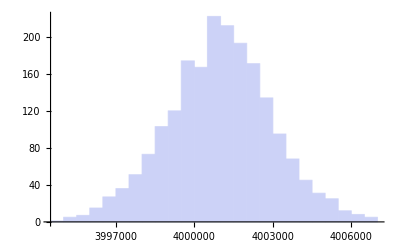

```mathematica
Histogram[Map[Tr[#]&,citedcitingTab]]
```

もし、自誌被引用数被引用数のうちで最大の数値ならつぎに大きな数値に置き換える、ただし、つぎに大きな数値が0でない場合

```mathematica
(citedcitingNextMaxSelfTab=nextMaxSelf[citedcitingTab])//Dimensions
```

{2000,2000}

合計値で正規化する

```mathematica
(citedcitingNextMaxSelfTabST=standerdizeSum[citedcitingNextMaxSelfTab]//N)//Dimensions
```

{2000,2000}

合計値が1になっていることの確認

```mathematica
Map[Tr[#]&,citedcitingNextMaxSelfTabST]//Chop//Union
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

PCA

```mathematica
citedcitingNextMaxSelfTabSTPCA=PrincipalComponents[citedcitingNextMaxSelfTabST];
```

第1、2、3軸でプロット

```mathematica
Graphics3D[Map[Point[#[[{1,2,3}]]]&,citedcitingNextMaxSelfTabSTPCA]]
```

-Graphics3D-

## test

```mathematica
testmat={{3,2,1},{1,2,2},{0,0,1}}
```

{{3,2,1},{1,2,2},{0,0,1}}

```mathematica
nextMaxSelf[testmat]
```

{{2,2,1},{1,2,2},{0,0,1}}

## おまけ(弾性衝突)

```mathematica
dp=0.5;rho=0.9*^3;gravdir={0,0,1};
pos=Module[{p,s,d,e,f,v,m=rho Pi dp^3/6,dt=3.*^-2},p=v={0,0,0};
Function[{gd},s=Clip[p]-p;(*壁との衝突*)d=-0.5*^3 Sign[s]^2 v;(*粘性力*)e=0.2*^6 Sign[s] Abs[s]^(3/2);(*弾性力*)f=d+e-m 9.8 Normalize[gd];(*力の合計*)v+=f/m dt;p+=v dt]];(*速度を算出して座標更新*)Graphics3D[Sphere[Dynamic[pos[gravdir]],dp/2],PlotRange->1+dp/2,SphericalRegion->True,ViewVertical->Dynamic[gravdir]]
```

-Graphics3D-

```mathematica
dp=0.5;rho=0.9*^3;gravdir={0,0,1};
pos=Module[{p,s,d,e,f,v,m=rho Pi dp^3/6,dt=3.*^-2},p=v={0,0,0};
Function[{gd},s=Clip[p]-p;(*壁との衝突*)d=-0.5*^3 Sign[s]^2 v;(*粘性力*)e=0.2*^6 Sign[s] Abs[s]^(3/2);(*弾性力*)f=d+e-m 9.8 Normalize[gd];(*力の合計*)v+=f/m dt;p+=v dt]];(*速度を算出して座標更新*)Graphics3D[Sphere[Dynamic[pos[gravdir]],dp/2],PlotRange->1+dp/2,SphericalRegion->True,ViewVertical->Dynamic[gravdir]]
```